# Parallel Raw Pattern Search: Remaining Geometries

This notebook runs the safeguarded raw parameter search for (5,0.5), (5,1.5), (5,2), (3,1), (7,1), and (10,1). The completed (5,1) trial is deliberately excluded. Each geometry warm-starts from its own stored production optimum, and its X and XX step sizes are scaled separately from those parameters.

The physics and integration estimator are unchanged from the successful (5,1) test. X uses the analytical kinetic correction and independently integrated Coulomb numerator and norm. XX retains raw P+Q, all six Coulomb terms, and all four kinetic contributions. Only the redundant global rotation is removed (phi_a = 0); all three remaining relative angles span [0,2 Pi]. There is no reflection folding, particle-exchange multiplicity, or shared fixed Sobol sample.

One global queue feeds eight parallel subkernels with candidates from all six geometries. A worker evaluates one complete parameter candidate at a time: its denominator followed by its numerator. Different candidates and geometries run concurrently, but the two integrals belonging to one candidate remain independent adaptive-QMC calls. The master kernel checkpoints every returned candidate. If a stage is interrupted, evaluate it again to submit only the missing candidates.

Run the cells in order. Unlike (5,1), these geometries have no compatible raw center evaluations to reuse, so their center points are included in both the search- and verification-budget stages.

## Load and review

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Main-State-Raw-Pattern-Search-Remaining-Geometries.wl"}]]
```

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

Remaining-geometry raw pattern-search campaign loaded for 6 geometries. Reusable candidates: 0. Review pscConfiguration[], then run pscPrepareKernels[].

```mathematica
pscConfiguration[]
```

<|implementation→parallel-raw-pattern-search-campaign-v1,geometries→{{5.,0.5},{5.,1.5},{5.,2.},{3.,1.},{7.,1.},{10.,1.}},workers→8,XBudget→2000000,XXSearchBudget→1000000,XXVerifyBudget→2000000,minimumImprovementRy→0.02,refinementDirectionCount→2,starts→<|5.|0.5→<|geometry→{5.,0.5},XAlpha→0.870939,XXParameters→{0.755694,0.213328,2.57748,2.38272},XSingleParticleRy→48.2438,XXSingleParticleRy→96.4876|>,5.|1.5→<|geometry→{5.,1.5},XAlpha→0.655699,XXParameters→{0.607794,0.00408921,2.85888,1.95328},XSingleParticleRy→6.00208,XXSingleParticleRy→12.0042|>,5.|2.→<|geometry→{5.,2.},XAlpha→0.604918,XXParameters→{0.587481,0.0105844,3.0206,1.87437},XSingleParticleRy→3.55664,XXSingleParticleRy→7.11328|>,3.|1.→<|geometry→{3.,1.},XAlpha→0.706089,XXParameters→{0.653302,0.063307,2.54218,2.29869},XSingleParticleRy→13.7453,XXSingleParticleRy→27.4906|>,7.|1.→<|geometry→{7.,1.},XAlpha→0.762339,XXParameters→{0.642364,0.0541802,2.83046,1.89635},XSingleParticleRy→12.3703,XXSingleParticleRy→24.7406|>,10.|1.→<|geometry→{10.,1.},XAlpha→0.759214,XXParameters→{0.642364,0.0541802,2.83046,1.89635},XSingleParticleRy→12.0609,XXSingleParticleRy→24.1219|>|>,geometryConfigurations→<|5.|0.5→<|geometry→{5.,0.5},XStartAlpha→0.870939,XStep→0.06,XInitialParameters→{{0.750939},{0.810939},{0.870939},{0.930939},{0.990939}},XXStartParameters→{0.755694,0.213328,2.57748,2.38272},XXSteps→{0.0906833,0.0533321,0.206199,0.238272},XXInitialParameters→{{0.755694,0.213328,2.57748,2.38272},{0.665011,0.213328,2.57748,2.38272},{0.846378,0.213328,2.57748,2.38272},{0.755694,0.159996,2.57748,2.38272},{0.755694,0.266661,2.57748,2.38272},{0.755694,0.213328,2.37129,2.38272},{0.755694,0.213328,2.78368,2.38272},{0.755694,0.213328,2.57748,2.14445},{0.755694,0.213328,2.57748,2.621}}|>,5.|1.5→<|geometry→{5.,1.5},XStartAlpha→0.655699,XStep→0.0458989,XInitialParameters→{{0.563901},{0.6098},{0.655699},{0.701598},{0.747497}},XXStartParameters→{0.607794,0.00408921,2.85888,1.95328},XXSteps→{0.0729353,0.02,0.22871,0.195328},XXInitialParameters→{{0.607794,0.00408921,2.85888,1.95328},{0.534859,0.00408921,2.85888,1.95328},{0.680729,0.00408921,2.85888,1.95328},{0.607794,0.001,2.85888,1.95328},{0.607794,0.0240892,2.85888,1.95328},{0.607794,0.00408921,2.63017,1.95328},{0.607794,0.00408921,3.08759,1.95328},{0.607794,0.00408921,2.85888,1.75795},{0.607794,0.00408921,2.85888,2.14861}}|>,5.|2.→<|geometry→{5.,2.},XStartAlpha→0.604918,XStep→0.0423442,XInitialParameters→{{0.520229},{0.562573},{0.604918},{0.647262},{0.689606}},XXStartParameters→{0.587481,0.0105844,3.0206,1.87437},XXSteps→{0.0704978,0.02,0.241648,0.187437},XXInitialParameters→{{0.587481,0.0105844,3.0206,1.87437},{0.516984,0.0105844,3.0206,1.87437},{0.657979,0.0105844,3.0206,1.87437},{0.587481,0.001,3.0206,1.87437},{0.587481,0.0305844,3.0206,1.87437},{0.587481,0.0105844,2.77895,1.87437},{0.587481,0.0105844,3.26225,1.87437},{0.587481,0.0105844,3.0206,1.68694},{0.587481,0.0105844,3.0206,2.06181}}|>,3.|1.→<|geometry→{3.,1.},XStartAlpha→0.706089,XStep→0.0494263,XInitialParameters→{{0.607237},{0.656663},{0.706089},{0.755516},{0.804942}},XXStartParameters→{0.653302,0.063307,2.54218,2.29869},XXSteps→{0.0783962,0.02,0.203375,0.229869},XXInitialParameters→{{0.653302,0.063307,2.54218,2.29869},{0.574906,0.063307,2.54218,2.29869},{0.731698,0.063307,2.54218,2.29869},{0.653302,0.043307,2.54218,2.29869},{0.653302,0.083307,2.54218,2.29869},{0.653302,0.063307,2.33881,2.29869},{0.653302,0.063307,2.74556,2.29869},{0.653302,0.063307,2.54218,2.06882},{0.653302,0.063307,2.54218,2.52856}}|>,7.|1.→<|geometry→{7.,1.},XStartAlpha→0.762339,XStep→0.0533638,XInitialParameters→{{0.655612},{0.708976},{0.762339},{0.815703},{0.869067}},XXStartParameters→{0.642364,0.0541802,2.83046,1.89635},XXSteps→{0.0770837,0.02,0.226437,0.189635},XXInitialParameters→{{0.642364,0.0541802,2.83046,1.89635},{0.565281,0.0541802,2.83046,1.89635},{0.719448,0.0541802,2.83046,1.89635},{0.642364,0.0341802,2.83046,1.89635},{0.642364,0.0741802,2.83046,1.89635},{0.642364,0.0541802,2.60403,1.89635},{0.642364,0.0541802,3.0569,1.89635},{0.642364,0.0541802,2.83046,1.70671},{0.642364,0.0541802,2.83046,2.08598}}|>,10.|1.→<|geometry→{10.,1.},XStartAlpha→0.759214,XStep→0.053145,XInitialParameters→{{0.652924},{0.706069},{0.759214},{0.812359},{0.865504}},XXStartParameters→{0.642364,0.0541802,2.83046,1.89635},XXSteps→{0.0770837,0.02,0.226437,0.189635},XXInitialParameters→{{0.642364,0.0541802,2.83046,1.89635},{0.565281,0.0541802,2.83046,1.89635},{0.719448,0.0541802,2.83046,1.89635},{0.642364,0.0341802,2.83046,1.89635},{0.642364,0.0741802,2.83046,1.89635},{0.642364,0.0541802,2.60403,1.89635},{0.642364,0.0541802,3.0569,1.89635},{0.642364,0.0541802,2.83046,1.70671},{0.642364,0.0541802,2.83046,2.08598}}|>|>,XKinetic→analytic alpha^2 (1 + m_e/m_h),angularTreatment→phi_a=0; all remaining relative angles cover [0,2 Pi],sampling→independent adaptive QMC calls for numerator and denominator|>

```mathematica
pscPrepareKernels[]
```

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

«5 more identical outputs»

Parallel workers prepared: 8. Campaign source loaded successfully on all workers: True

<|processorCount→10,kernelCount→8,loaded→True|>

## Exciton scans

The initial cell queues five 2,000,000-point alpha values for every geometry. The refinement cell then queues two half-step values around each geometry's best initial point.

```mathematica
pscRunXInitial[]
```

X-initial-grid: 30 requested; 30 missing; 0 reused.

X-initial-grid: completed (5.|0.5) 0.7509392140222256 on kernel 19; correction = -3.28405; remaining = 29

X-initial-grid: completed (5.|1.5) 0.5639009538682851 on kernel 24; correction = -1.91498; remaining = 28

X-initial-grid: completed (5.|1.5) 0.6556987835677733 on kernel 26; correction = -1.92127; remaining = 27

X-initial-grid: completed (5.|0.5) 0.8709392140222256 on kernel 21; correction = -3.27553; remaining = 26

X-initial-grid: completed (5.|0.5) 0.8109392140222256 on kernel 20; correction = -3.28195; remaining = 25

X-initial-grid: completed (5.|0.5) 0.9309392140222257 on kernel 22; correction = -3.26935; remaining = 24

X-initial-grid: completed (5.|0.5) 0.9909392140222256 on kernel 23; correction = -3.2455; remaining = 23

X-initial-grid: completed (5.|1.5) 0.6097998687180292 on kernel 25; correction = -1.92272; remaining = 22

X-initial-grid: completed (5.|1.5) 0.7015976984175175 on kernel 19; correction = -1.92303; remaining = 21

X-initial-grid: completed (5.|1.5) 0.7474966132672616 on kernel 24; correction = -1.91398; remaining = 20

X-initial-grid: completed (5.|2.) 0.5202290788682852 on kernel 26; correction = -1.65485; remaining = 19

X-initial-grid: completed (5.|2.) 0.5625733062180293 on kernel 21; correction = -1.66298; remaining = 18

X-initial-grid: completed (5.|2.) 0.6049175335677734 on kernel 20; correction = -1.66754; remaining = 17

X-initial-grid: completed (5.|2.) 0.6896059882672617 on kernel 23; correction = -1.66118; remaining = 16

X-initial-grid: completed (5.|2.) 0.6472617609175176 on kernel 22; correction = -1.66382; remaining = 15

X-initial-grid: completed (3.|1.) 0.607236891368285 on kernel 25; correction = -2.70602; remaining = 14

X-initial-grid: completed (3.|1.) 0.6566631499680291 on kernel 19; correction = -2.70781; remaining = 13

X-initial-grid: completed (3.|1.) 0.7060894085677732 on kernel 24; correction = -2.70988; remaining = 12

X-initial-grid: completed (3.|1.) 0.7555156671675174 on kernel 26; correction = -2.7022; remaining = 11

X-initial-grid: completed (3.|1.) 0.8049419257672615 on kernel 21; correction = -2.6922; remaining = 10

X-initial-grid: completed (7.|1.) 0.655611891368285 on kernel 20; correction = -2.15875; remaining = 9

X-initial-grid: completed (7.|1.) 0.7089756499680291 on kernel 23; correction = -2.16463; remaining = 8

X-initial-grid: completed (7.|1.) 0.7623394085677733 on kernel 22; correction = -2.16467; remaining = 7

X-initial-grid: completed (7.|1.) 0.8157031671675175 on kernel 25; correction = -2.15296; remaining = 6

X-initial-grid: completed (10.|1.) 0.652924391368285 on kernel 24; correction = -1.98184; remaining = 5

X-initial-grid: completed (7.|1.) 0.8690669257672615 on kernel 19; correction = -2.13935; remaining = 4

X-initial-grid: completed (10.|1.) 0.7060693999680291 on kernel 26; correction = -1.99074; remaining = 3

X-initial-grid: completed (10.|1.) 0.8123594171675174 on kernel 20; correction = -1.99108; remaining = 2

X-initial-grid: completed (10.|1.) 0.7592144085677732 on kernel 21; correction = -1.99706; remaining = 1

X-initial-grid: completed (10.|1.) 0.8655044257672615 on kernel 23; correction = -1.97343; remaining = 0

{<|candidateKey→5.|0.5::X::2000000::0.7509392140222256,stage→X-initial-grid,geometryKey→5.|0.5,a→5.,c→0.5,system→X,budget→2000000,parameters→{0.750939},parameterKey→0.7509392140222256,norm→0.250971,numeratorRy→-0.986799,analyticKineticRy→0.64787,correctionRy→-3.28405,roughCorrectionErrorRy→0.00643971,singleParticleRy→48.2438,totalRy→44.9597,elapsedSeconds→522.088,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:21,integrals→{<|integral→normDenominator,seconds→191.833,value→0.250971,hitMaxPoints→True,relativeErrorEstimate→0.00062751,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.250971 and 0.000157487
     for the integral and error estimates.,messageIntegralEstimate→0.250971,reportedErrorEstimate→0.000157487|>,<|integral→coulombNumerator,seconds→330.255,value→-0.986799,hitMaxPoints→True,relativeErrorEstimate→0.00151282,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.986799 and 0.00149285
     for the integral and error estimates.,messageIntegralEstimate→-0.986799,reportedErrorEstimate→0.00149285|>}|>,<|candidateKey→5.|0.5::X::2000000::0.8109392140222256,stage→X-initial-grid,geometryKey→5.|0.5,a→5.,c→0.5,system→X,budget→2000000,parameters→{0.810939},parameterKey→0.8109392140222256,norm→0.229668,numeratorRy→-0.927281,analyticKineticRy→0.755535,correctionRy→-3.28195,roughCorrectionErrorRy→0.00693097,singleParticleRy→48.2438,totalRy→44.9618,elapsedSeconds→525.501,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:24,integrals→{<|integral→normDenominator,seconds→192.762,value→0.229668,hitMaxPoints→True,relativeErrorEstimate→0.0006689,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.229668 and 0.000153625
     for the integral and error estimates.,messageIntegralEstimate→0.229668,reportedErrorEstimate→0.000153625|>,<|integral→coulombNumerator,seconds→332.739,value→-0.927281,hitMaxPoints→True,relativeErrorEstimate→0.00158098,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.927281 and 0.00146601
     for the integral and error estimates.,messageIntegralEstimate→-0.927281,reportedErrorEstimate→0.00146601|>}|>,<|candidateKey→5.|0.5::X::2000000::0.8709392140222256,stage→X-initial-grid,geometryKey→5.|0.5,a→5.,c→0.5,system→X,budget→2000000,parameters→{0.870939},parameterKey→0.8709392140222256,norm→0.210691,numeratorRy→-0.873736,analyticKineticRy→0.871473,correctionRy→-3.27553,roughCorrectionErrorRy→0.00738534,singleParticleRy→48.2438,totalRy→44.9683,elapsedSeconds→524.89,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:23,integrals→{<|integral→normDenominator,seconds→192.881,value→0.210691,hitMaxPoints→True,relativeErrorEstimate→0.000712565,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.210691 and 0.000150131
     for the integral and error estimates.,messageIntegralEstimate→0.210691,reportedErrorEstimate→0.000150131|>,<|integral→coulombNumerator,seconds→332.009,value→-0.873736,hitMaxPoints→True,relativeErrorEstimate→0.00163212,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.873736 and 0.00142604
     for the integral and error estimates.,messageIntegralEstimate→-0.873736,reportedErrorEstimate→0.00142604|>}|>,<|candidateKey→5.|0.5::X::2000000::0.9309392140222257,stage→X-initial-grid,geometryKey→5.|0.5,a→5.,c→0.5,system→X,budget→2000000,parameters→{0.930939},parameterKey→0.9309392140222257,norm→0.193775,numeratorRy→-0.826455,analyticKineticRy→0.995682,correctionRy→-3.26935,roughCorrectionErrorRy→0.00790137,singleParticleRy→48.2438,totalRy→44.9744,elapsedSeconds→525.565,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:24,integrals→{<|integral→normDenominator,seconds→193.487,value→0.193775,hitMaxPoints→True,relativeErrorEstimate→0.000753891,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.193775 and 0.000146085
     for the integral and error estimates.,messageIntegralEstimate→0.193775,reportedErrorEstimate→0.000146085|>,<|integral→coulombNumerator,seconds→332.078,value→-0.826455,hitMaxPoints→True,relativeErrorEstimate→0.00169226,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.826455 and 0.00139858
     for the integral and error estimates.,messageIntegralEstimate→-0.826455,reportedErrorEstimate→0.00139858|>}|>,<|candidateKey→5.|0.5::X::2000000::0.9909392140222256,stage→X-initial-grid,geometryKey→5.|0.5,a→5.,c→0.5,system→X,budget→2000000,parameters→{0.990939},parameterKey→0.9909392140222256,norm→0.178572,numeratorRy→-0.781012,analyticKineticRy→1.12816,correctionRy→-3.2455,roughCorrectionErrorRy→0.00839709,singleParticleRy→48.2438,totalRy→44.9983,elapsedSeconds→525.673,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:24,integrals→{<|integral→normDenominator,seconds→192.857,value→0.178572,hitMaxPoints→True,relativeErrorEstimate→0.000799601,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.178572 and 0.000142786
     for the integral and error estimates.,messageIntegralEstimate→0.178572,reportedErrorEstimate→0.000142786|>,<|integral→coulombNumerator,seconds→332.816,value→-0.781012,hitMaxPoints→True,relativeErrorEstimate→0.00174549,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.781012 and 0.00136325
     for the integral and error estimates.,messageIntegralEstimate→-0.781012,reportedErrorEstimate→0.00136325|>}|>,<|candidateKey→5.|1.5::X::2000000::0.5639009538682851,stage→X-initial-grid,geometryKey→5.|1.5,a→5.,c→1.5,system→X,budget→2000000,parameters→{0.563901},parameterKey→0.5639009538682851,norm→0.173572,numeratorRy→-0.395797,analyticKineticRy→0.365329,correctionRy→-1.91498,roughCorrectionErrorRy→0.0041666,singleParticleRy→6.00208,totalRy→4.0871,elapsedSeconds→522.801,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:21,integrals→{<|integral→normDenominator,seconds→191.983,value→0.173572,hitMaxPoints→True,relativeErrorEstimate→0.00078068,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.173572 and 0.000135504
     for the integral and error estimates.,messageIntegralEstimate→0.173572,reportedErrorEstimate→0.000135504|>,<|integral→coulombNumerator,seconds→330.818,value→-0.395797,hitMaxPoints→True,relativeErrorEstimate→0.00165204,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.395797 and 0.000653872
     for the integral and error estimates.,messageIntegralEstimate→-0.395797,reportedErrorEstimate→0.000653872|>}|>,<|candidateKey→5.|1.5::X::2000000::0.6097998687180292,stage→X-initial-grid,geometryKey→5.|1.5,a→5.,c→1.5,system→X,budget→2000000,parameters→{0.6098},parameterKey→0.6097998687180292,norm→0.155449,numeratorRy→-0.365296,analyticKineticRy→0.427221,correctionRy→-1.92272,roughCorrectionErrorRy→0.00448706,singleParticleRy→6.00208,totalRy→4.07936,elapsedSeconds→528.353,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:27,integrals→{<|integral→normDenominator,seconds→193.886,value→0.155449,hitMaxPoints→True,relativeErrorEstimate→0.000838856,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.155449 and 0.000130399
     for the integral and error estimates.,messageIntegralEstimate→0.155449,reportedErrorEstimate→0.000130399|>,<|integral→coulombNumerator,seconds→334.468,value→-0.365296,hitMaxPoints→True,relativeErrorEstimate→0.0017153,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.365296 and 0.000626591
     for the integral and error estimates.,messageIntegralEstimate→-0.365296,reportedErrorEstimate→0.000626591|>}|>,<|candidateKey→5.|1.5::X::2000000::0.6556987835677733,stage→X-initial-grid,geometryKey→5.|1.5,a→5.,c→1.5,system→X,budget→2000000,parameters→{0.655699},parameterKey→0.6556987835677733,norm→0.139726,numeratorRy→-0.33747,analyticKineticRy→0.493954,correctionRy→-1.92127,roughCorrectionErrorRy→0.00483381,singleParticleRy→6.00208,totalRy→4.08081,elapsedSeconds→522.802,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:10:38,completed→2026-08-01T13:19:21,integrals→{<|integral→normDenominator,seconds→192.76,value→0.139726,hitMaxPoints→True,relativeErrorEstimate→0.000894292,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.139726 and 0.000124956
     for the integral and error estimates.,messageIntegralEstimate→0.139726,reportedErrorEstimate→0.000124956|>,<|integral→coulombNumerator,seconds→330.042,value→-0.33747,hitMaxPoints→True,relativeErrorEstimate→0.00179048,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.33747 and 0.000604233
     for the integral and error estimates.,messageIntegralEstimate→-0.33747,reportedErrorEstimate→0.000604233|>}|>,<|candidateKey→5.|1.5::X::2000000::0.7015976984175175,stage→X-initial-grid,geometryKey→5.|1.5,a→5.,c→1.5,system→X,budget→2000000,parameters→{0.701598},parameterKey→0.7015976984175175,norm→0.125991,numeratorRy→-0.313535,analyticKineticRy→0.565528,correctionRy→-1.92303,roughCorrectionErrorRy→0.00523608,singleParticleRy→6.00208,totalRy→4.07905,elapsedSeconds→551.541,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:21,completed→2026-08-01T13:28:32,integrals→{<|integral→normDenominator,seconds→232.235,value→0.125991,hitMaxPoints→True,relativeErrorEstimate→0.000956228,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.125991 and 0.000120476
     for the integral and error estimates.,messageIntegralEstimate→0.125991,reportedErrorEstimate→0.000120476|>,<|integral→coulombNumerator,seconds→319.307,value→-0.313535,hitMaxPoints→True,relativeErrorEstimate→0.00187422,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.313535 and 0.000587635
     for the integral and error estimates.,messageIntegralEstimate→-0.313535,reportedErrorEstimate→0.000587635|>}|>,<|candidateKey→5.|1.5::X::2000000::0.7474966132672616,stage→X-initial-grid,geometryKey→5.|1.5,a→5.,c→1.5,system→X,budget→2000000,parameters→{0.747497},parameterKey→0.7474966132672616,norm→0.113942,numeratorRy→-0.291226,analyticKineticRy→0.641943,correctionRy→-1.91398,roughCorrectionErrorRy→0.00559652,singleParticleRy→6.00208,totalRy→4.0881,elapsedSeconds→551.182,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:21,completed→2026-08-01T13:28:33,integrals→{<|integral→normDenominator,seconds→232.536,value→0.113942,hitMaxPoints→True,relativeErrorEstimate→0.00101034,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.113942 and 0.00011512
     for the integral and error estimates.,messageIntegralEstimate→0.113942,reportedErrorEstimate→0.00011512|>,<|integral→coulombNumerator,seconds→318.646,value→-0.291226,hitMaxPoints→True,relativeErrorEstimate→0.0019426,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.291226 and 0.000565735
     for the integral and error estimates.,messageIntegralEstimate→-0.291226,reportedErrorEstimate→0.000565735|>}|>,<|candidateKey→5.|2.::X::2000000::0.5202290788682852,stage→X-initial-grid,geometryKey→5.|2.,a→5.,c→2.,system→X,budget→2000000,parameters→{0.520229},parameterKey→0.5202290788682852,norm→0.155452,numeratorRy→-0.305585,analyticKineticRy→0.310933,correctionRy→-1.65485,roughCorrectionErrorRy→0.00371129,singleParticleRy→3.55664,totalRy→1.90179,elapsedSeconds→551.493,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:21,completed→2026-08-01T13:28:33,integrals→{<|integral→normDenominator,seconds→232.286,value→0.155452,hitMaxPoints→True,relativeErrorEstimate→0.000829284,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.155452 and 0.000128914
     for the integral and error estimates.,messageIntegralEstimate→0.155452,reportedErrorEstimate→0.000128914|>,<|integral→coulombNumerator,seconds→319.207,value→-0.305585,hitMaxPoints→True,relativeErrorEstimate→0.00169606,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.305585 and 0.000518291
     for the integral and error estimates.,messageIntegralEstimate→-0.305585,reportedErrorEstimate→0.000518291|>}|>,<|candidateKey→5.|2.::X::2000000::0.5625733062180293,stage→X-initial-grid,geometryKey→5.|2.,a→5.,c→2.,system→X,budget→2000000,parameters→{0.562573},parameterKey→0.5625733062180293,norm→0.13842,numeratorRy→-0.280522,analyticKineticRy→0.36361,correctionRy→-1.66298,roughCorrectionErrorRy→0.00402136,singleParticleRy→3.55664,totalRy→1.89365,elapsedSeconds→553.89,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:23,completed→2026-08-01T13:28:37,integrals→{<|integral→normDenominator,seconds→232.72,value→0.13842,hitMaxPoints→True,relativeErrorEstimate→0.000882378,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.13842 and 0.000122139
     for the integral and error estimates.,messageIntegralEstimate→0.13842,reportedErrorEstimate→0.000122139|>,<|integral→coulombNumerator,seconds→321.17,value→-0.280522,hitMaxPoints→True,relativeErrorEstimate→0.00177731,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.280522 and 0.000498574
     for the integral and error estimates.,messageIntegralEstimate→-0.280522,reportedErrorEstimate→0.000498574|>}|>,<|candidateKey→5.|2.::X::2000000::0.6049175335677734,stage→X-initial-grid,geometryKey→5.|2.,a→5.,c→2.,system→X,budget→2000000,parameters→{0.604918},parameterKey→0.6049175335677734,norm→0.123688,numeratorRy→-0.258254,analyticKineticRy→0.420407,correctionRy→-1.66754,roughCorrectionErrorRy→0.00434214,singleParticleRy→3.55664,totalRy→1.8891,elapsedSeconds→554.234,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:24,completed→2026-08-01T13:28:38,integrals→{<|integral→normDenominator,seconds→233.358,value→0.123688,hitMaxPoints→True,relativeErrorEstimate→0.000953275,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.123688 and 0.000117909
     for the integral and error estimates.,messageIntegralEstimate→0.123688,reportedErrorEstimate→0.000117909|>,<|integral→coulombNumerator,seconds→320.876,value→-0.258254,hitMaxPoints→True,relativeErrorEstimate→0.00184827,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.258254 and 0.000477324
     for the integral and error estimates.,messageIntegralEstimate→-0.258254,reportedErrorEstimate→0.000477324|>}|>,<|candidateKey→5.|2.::X::2000000::0.6472617609175176,stage→X-initial-grid,geometryKey→5.|2.,a→5.,c→2.,system→X,budget→2000000,parameters→{0.647262},parameterKey→0.6472617609175176,norm→0.110938,numeratorRy→-0.237978,analyticKineticRy→0.481324,correctionRy→-1.66382,roughCorrectionErrorRy→0.00466041,singleParticleRy→3.55664,totalRy→1.89282,elapsedSeconds→555.577,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:24,completed→2026-08-01T13:28:40,integrals→{<|integral→normDenominator,seconds→234.104,value→0.110938,hitMaxPoints→True,relativeErrorEstimate→0.00101382,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.110938 and 0.000112471
     for the integral and error estimates.,messageIntegralEstimate→0.110938,reportedErrorEstimate→0.000112471|>,<|integral→coulombNumerator,seconds→321.473,value→-0.237978,hitMaxPoints→True,relativeErrorEstimate→0.00192149,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.237978 and 0.000457272
     for the integral and error estimates.,messageIntegralEstimate→-0.237978,reportedErrorEstimate→0.000457272|>}|>,<|candidateKey→5.|2.::X::2000000::0.6896059882672617,stage→X-initial-grid,geometryKey→5.|2.,a→5.,c→2.,system→X,budget→2000000,parameters→{0.689606},parameterKey→0.6896059882672617,norm→0.0998259,numeratorRy→-0.220369,analyticKineticRy→0.546361,correctionRy→-1.66118,roughCorrectionErrorRy→0.00500303,singleParticleRy→3.55664,totalRy→1.89546,elapsedSeconds→554.368,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:24,completed→2026-08-01T13:28:39,integrals→{<|integral→normDenominator,seconds→233.065,value→0.0998259,hitMaxPoints→True,relativeErrorEstimate→0.00106592,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.0998259 and 0.000106406
     for the integral and error estimates.,messageIntegralEstimate→0.0998259,reportedErrorEstimate→0.000106406|>,<|integral→coulombNumerator,seconds→321.303,value→-0.220369,hitMaxPoints→True,relativeErrorEstimate→0.00200003,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.220369 and 0.000440745
     for the integral and error estimates.,messageIntegralEstimate→-0.220369,reportedErrorEstimate→0.000440745|>}|>,<|candidateKey→3.|1.::X::2000000::0.607236891368285,stage→X-initial-grid,geometryKey→3.|1.,a→3.,c→1.,system→X,budget→2000000,parameters→{0.607237},parameterKey→0.607236891368285,norm→0.276521,numeratorRy→-0.865416,analyticKineticRy→0.423637,correctionRy→-2.70602,roughCorrectionErrorRy→0.00452757,singleParticleRy→13.7453,totalRy→11.0393,elapsedSeconds→555.291,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:19:27,completed→2026-08-01T13:28:42,integrals→{<|integral→normDenominator,seconds→233.774,value→0.276521,hitMaxPoints→True,relativeErrorEstimate→0.000555188,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.276521 and 0.000153521
     for the integral and error estimates.,messageIntegralEstimate→0.276521,reportedErrorEstimate→0.000153521|>,<|integral→coulombNumerator,seconds→321.517,value→-0.865416,hitMaxPoints→True,relativeErrorEstimate→0.00133589,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.865416 and 0.0011561
     for the integral and error estimates.,messageIntegralEstimate→-0.865416,reportedErrorEstimate→0.0011561|>}|>,<|candidateKey→3.|1.::X::2000000::0.6566631499680291,stage→X-initial-grid,geometryKey→3.|1.,a→3.,c→1.,system→X,budget→2000000,parameters→{0.656663},parameterKey→0.6566631499680291,norm→0.253487,numeratorRy→-0.811974,analyticKineticRy→0.495408,correctionRy→-2.70781,roughCorrectionErrorRy→0.00484423,singleParticleRy→13.7453,totalRy→11.0375,elapsedSeconds→566.439,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:32,completed→2026-08-01T13:37:59,integrals→{<|integral→normDenominator,seconds→233.386,value→0.253487,hitMaxPoints→True,relativeErrorEstimate→0.000594472,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.253487 and 0.000150691
     for the integral and error estimates.,messageIntegralEstimate→0.253487,reportedErrorEstimate→0.000150691|>,<|integral→coulombNumerator,seconds→333.053,value→-0.811974,hitMaxPoints→True,relativeErrorEstimate→0.00139056,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.811974 and 0.0011291
     for the integral and error estimates.,messageIntegralEstimate→-0.811974,reportedErrorEstimate→0.0011291|>}|>,<|candidateKey→3.|1.::X::2000000::0.7060894085677732,stage→X-initial-grid,geometryKey→3.|1.,a→3.,c→1.,system→X,budget→2000000,parameters→{0.706089},parameterKey→0.7060894085677732,norm→0.232865,numeratorRy→-0.764421,analyticKineticRy→0.572793,correctionRy→-2.70988,roughCorrectionErrorRy→0.00519179,singleParticleRy→13.7453,totalRy→11.0354,elapsedSeconds→566.244,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:33,completed→2026-08-01T13:37:59,integrals→{<|integral→normDenominator,seconds→233.271,value→0.232865,hitMaxPoints→True,relativeErrorEstimate→0.000635818,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.232865 and 0.00014806
     for the integral and error estimates.,messageIntegralEstimate→0.232865,reportedErrorEstimate→0.00014806|>,<|integral→coulombNumerator,seconds→332.974,value→-0.764421,hitMaxPoints→True,relativeErrorEstimate→0.00144814,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.764421 and 0.00110699
     for the integral and error estimates.,messageIntegralEstimate→-0.764421,reportedErrorEstimate→0.00110699|>}|>,<|candidateKey→3.|1.::X::2000000::0.7555156671675174,stage→X-initial-grid,geometryKey→3.|1.,a→3.,c→1.,system→X,budget→2000000,parameters→{0.755516},parameterKey→0.7555156671675174,norm→0.21436,numeratorRy→-0.719818,analyticKineticRy→0.65579,correctionRy→-2.7022,roughCorrectionErrorRy→0.00549191,singleParticleRy→13.7453,totalRy→11.0431,elapsedSeconds→568.346,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:33,completed→2026-08-01T13:38:01,integrals→{<|integral→normDenominator,seconds→233.534,value→0.21436,hitMaxPoints→True,relativeErrorEstimate→0.000671404,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.21436 and 0.000143922
     for the integral and error estimates.,messageIntegralEstimate→0.21436,reportedErrorEstimate→0.000143922|>,<|integral→coulombNumerator,seconds→334.812,value→-0.719818,hitMaxPoints→True,relativeErrorEstimate→0.00149131,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.719818 and 0.00107347
     for the integral and error estimates.,messageIntegralEstimate→-0.719818,reportedErrorEstimate→0.00107347|>}|>,<|candidateKey→3.|1.::X::2000000::0.8049419257672615,stage→X-initial-grid,geometryKey→3.|1.,a→3.,c→1.,system→X,budget→2000000,parameters→{0.804942},parameterKey→0.8049419257672615,norm→0.197719,numeratorRy→-0.679483,analyticKineticRy→0.744401,correctionRy→-2.6922,roughCorrectionErrorRy→0.00586711,singleParticleRy→13.7453,totalRy→11.0531,elapsedSeconds→567.609,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:37,completed→2026-08-01T13:38:05,integrals→{<|integral→normDenominator,seconds→233.148,value→0.197719,hitMaxPoints→True,relativeErrorEstimate→0.000711119,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.197719 and 0.000140602
     for the integral and error estimates.,messageIntegralEstimate→0.197719,reportedErrorEstimate→0.000140602|>,<|integral→coulombNumerator,seconds→334.46,value→-0.679483,hitMaxPoints→True,relativeErrorEstimate→0.00155209,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.679483 and 0.00105462
     for the integral and error estimates.,messageIntegralEstimate→-0.679483,reportedErrorEstimate→0.00105462|>}|>,<|candidateKey→7.|1.::X::2000000::0.655611891368285,stage→X-initial-grid,geometryKey→7.|1.,a→7.,c→1.,system→X,budget→2000000,parameters→{0.655612},parameterKey→0.655611891368285,norm→0.153339,numeratorRy→-0.406744,analyticKineticRy→0.493823,correctionRy→-2.15875,roughCorrectionErrorRy→0.00534762,singleParticleRy→12.3703,totalRy→10.2116,elapsedSeconds→567.303,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:38,completed→2026-08-01T13:38:06,integrals→{<|integral→normDenominator,seconds→233.111,value→0.153339,hitMaxPoints→True,relativeErrorEstimate→0.000870567,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.153339 and 0.000133492
     for the integral and error estimates.,messageIntegralEstimate→0.153339,reportedErrorEstimate→0.000133492|>,<|integral→coulombNumerator,seconds→334.192,value→-0.406744,hitMaxPoints→True,relativeErrorEstimate→0.00181835,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.406744 and 0.000739604
     for the integral and error estimates.,messageIntegralEstimate→-0.406744,reportedErrorEstimate→0.000739604|>}|>,<|candidateKey→7.|1.::X::2000000::0.7089756499680291,stage→X-initial-grid,geometryKey→7.|1.,a→7.,c→1.,system→X,budget→2000000,parameters→{0.708976},parameterKey→0.7089756499680291,norm→0.136899,numeratorRy→-0.375393,analyticKineticRy→0.577485,correctionRy→-2.16463,roughCorrectionErrorRy→0.00579794,singleParticleRy→12.3703,totalRy→10.2057,elapsedSeconds→568.534,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:39,completed→2026-08-01T13:38:07,integrals→{<|integral→normDenominator,seconds→232.875,value→0.136899,hitMaxPoints→True,relativeErrorEstimate→0.000938274,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.136899 and 0.000128449
     for the integral and error estimates.,messageIntegralEstimate→0.136899,reportedErrorEstimate→0.000128449|>,<|integral→coulombNumerator,seconds→335.659,value→-0.375393,hitMaxPoints→True,relativeErrorEstimate→0.00189482,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.375393 and 0.000711304
     for the integral and error estimates.,messageIntegralEstimate→-0.375393,reportedErrorEstimate→0.000711304|>}|>,<|candidateKey→7.|1.::X::2000000::0.7623394085677733,stage→X-initial-grid,geometryKey→7.|1.,a→7.,c→1.,system→X,budget→2000000,parameters→{0.762339},parameterKey→0.7623394085677733,norm→0.122686,numeratorRy→-0.347491,analyticKineticRy→0.66769,correctionRy→-2.16467,roughCorrectionErrorRy→0.00627645,singleParticleRy→12.3703,totalRy→10.2057,elapsedSeconds→569.27,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:40,completed→2026-08-01T13:38:09,integrals→{<|integral→normDenominator,seconds→233.993,value→0.122686,hitMaxPoints→True,relativeErrorEstimate→0.000994816,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.122686 and 0.00012205
     for the integral and error estimates.,messageIntegralEstimate→0.122686,reportedErrorEstimate→0.00012205|>,<|integral→coulombNumerator,seconds→335.277,value→-0.347491,hitMaxPoints→True,relativeErrorEstimate→0.00198013,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.347491 and 0.000688077
     for the integral and error estimates.,messageIntegralEstimate→-0.347491,reportedErrorEstimate→0.000688077|>}|>,<|candidateKey→7.|1.::X::2000000::0.8157031671675175,stage→X-initial-grid,geometryKey→7.|1.,a→7.,c→1.,system→X,budget→2000000,parameters→{0.815703},parameterKey→0.8157031671675175,norm→0.110415,numeratorRy→-0.322125,analyticKineticRy→0.764438,correctionRy→-2.15296,roughCorrectionErrorRy→0.00674239,singleParticleRy→12.3703,totalRy→10.2174,elapsedSeconds→570.422,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:28:42,completed→2026-08-01T13:38:13,integrals→{<|integral→normDenominator,seconds→234.688,value→0.110415,hitMaxPoints→True,relativeErrorEstimate→0.00106964,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.110415 and 0.000118105
     for the integral and error estimates.,messageIntegralEstimate→0.110415,reportedErrorEstimate→0.000118105|>,<|integral→coulombNumerator,seconds→335.734,value→-0.322125,hitMaxPoints→True,relativeErrorEstimate→0.00204867,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.322125 and 0.000659929
     for the integral and error estimates.,messageIntegralEstimate→-0.322125,reportedErrorEstimate→0.000659929|>}|>,<|candidateKey→7.|1.::X::2000000::0.8690669257672615,stage→X-initial-grid,geometryKey→7.|1.,a→7.,c→1.,system→X,budget→2000000,parameters→{0.869067},parameterKey→0.8690669257672615,norm→0.0996798,numeratorRy→-0.299745,analyticKineticRy→0.86773,correctionRy→-2.13935,roughCorrectionErrorRy→0.00722301,singleParticleRy→12.3703,totalRy→10.231,elapsedSeconds→469.498,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:37:59,completed→2026-08-01T13:45:48,integrals→{<|integral→normDenominator,seconds→200.019,value→0.0996798,hitMaxPoints→True,relativeErrorEstimate→0.00111746,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.0996798 and 0.000111388
     for the integral and error estimates.,messageIntegralEstimate→0.0996798,reportedErrorEstimate→0.000111388|>,<|integral→coulombNumerator,seconds→269.479,value→-0.299745,hitMaxPoints→True,relativeErrorEstimate→0.00212624,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.299745 and 0.00063733
     for the integral and error estimates.,messageIntegralEstimate→-0.299745,reportedErrorEstimate→0.00063733|>}|>,<|candidateKey→10.|1.::X::2000000::0.652924391368285,stage→X-initial-grid,geometryKey→10.|1.,a→10.,c→1.,system→X,budget→2000000,parameters→{0.652924},parameterKey→0.652924391368285,norm→0.120374,numeratorRy→-0.297519,analyticKineticRy→0.489783,correctionRy→-1.98184,roughCorrectionErrorRy→0.00562453,singleParticleRy→12.0609,totalRy→10.0791,elapsedSeconds→467.324,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:37:59,completed→2026-08-01T13:45:46,integrals→{<|integral→normDenominator,seconds→198.555,value→0.120374,hitMaxPoints→True,relativeErrorEstimate→0.00102489,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.120374 and 0.00012337
     for the integral and error estimates.,messageIntegralEstimate→0.120374,reportedErrorEstimate→0.00012337|>,<|integral→coulombNumerator,seconds→268.769,value→-0.297519,hitMaxPoints→True,relativeErrorEstimate→0.00203179,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.297519 and 0.000604495
     for the integral and error estimates.,messageIntegralEstimate→-0.297519,reportedErrorEstimate→0.000604495|>}|>,<|candidateKey→10.|1.::X::2000000::0.7060693999680291,stage→X-initial-grid,geometryKey→10.|1.,a→10.,c→1.,system→X,budget→2000000,parameters→{0.706069},parameterKey→0.7060693999680291,norm→0.106548,numeratorRy→-0.273137,analyticKineticRy→0.57276,correctionRy→-1.99074,roughCorrectionErrorRy→0.00616552,singleParticleRy→12.0609,totalRy→10.0702,elapsedSeconds→467.46,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:38:01,completed→2026-08-01T13:45:49,integrals→{<|integral→normDenominator,seconds→199.042,value→0.106548,hitMaxPoints→True,relativeErrorEstimate→0.00110297,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.106548 and 0.000117519
     for the integral and error estimates.,messageIntegralEstimate→0.106548,reportedErrorEstimate→0.000117519|>,<|integral→coulombNumerator,seconds→268.417,value→-0.273137,hitMaxPoints→True,relativeErrorEstimate→0.0021373,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.273137 and 0.000583774
     for the integral and error estimates.,messageIntegralEstimate→-0.273137,reportedErrorEstimate→0.000583774|>}|>,<|candidateKey→10.|1.::X::2000000::0.7592144085677732,stage→X-initial-grid,geometryKey→10.|1.,a→10.,c→1.,system→X,budget→2000000,parameters→{0.759214},parameterKey→0.7592144085677732,norm→0.0947698,numeratorRy→-0.25202,analyticKineticRy→0.662227,correctionRy→-1.99706,roughCorrectionErrorRy→0.00666068,singleParticleRy→12.0609,totalRy→10.0639,elapsedSeconds→466.997,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:38:05,completed→2026-08-01T13:45:52,integrals→{<|integral→normDenominator,seconds→198.108,value→0.0947698,hitMaxPoints→True,relativeErrorEstimate→0.00118049,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.0947698 and 0.000111875
     for the integral and error estimates.,messageIntegralEstimate→0.0947698,reportedErrorEstimate→0.000111875|>,<|integral→coulombNumerator,seconds→268.889,value→-0.25202,hitMaxPoints→True,relativeErrorEstimate→0.00220905,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.25202 and 0.000556725
     for the integral and error estimates.,messageIntegralEstimate→-0.25202,reportedErrorEstimate→0.000556725|>}|>,<|candidateKey→10.|1.::X::2000000::0.8123594171675174,stage→X-initial-grid,geometryKey→10.|1.,a→10.,c→1.,system→X,budget→2000000,parameters→{0.812359},parameterKey→0.8123594171675174,norm→0.0846733,numeratorRy→-0.232789,analyticKineticRy→0.758184,correctionRy→-1.99108,roughCorrectionErrorRy→0.00724345,singleParticleRy→12.0609,totalRy→10.0699,elapsedSeconds→466.216,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:38:06,completed→2026-08-01T13:45:52,integrals→{<|integral→normDenominator,seconds→198.166,value→0.0846733,hitMaxPoints→True,relativeErrorEstimate→0.0012553,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.0846733 and 0.00010629
     for the integral and error estimates.,messageIntegralEstimate→0.0846733,reportedErrorEstimate→0.00010629|>,<|integral→coulombNumerator,seconds→268.05,value→-0.232789,hitMaxPoints→True,relativeErrorEstimate→0.00231642,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.232789 and 0.000539238
     for the integral and error estimates.,messageIntegralEstimate→-0.232789,reportedErrorEstimate→0.000539238|>}|>,<|candidateKey→10.|1.::X::2000000::0.8655044257672615,stage→X-initial-grid,geometryKey→10.|1.,a→10.,c→1.,system→X,budget→2000000,parameters→{0.865504},parameterKey→0.8655044257672615,norm→0.0759152,numeratorRy→-0.215148,analyticKineticRy→0.86063,correctionRy→-1.97343,roughCorrectionErrorRy→0.00774556,singleParticleRy→12.0609,totalRy→10.0875,elapsedSeconds→465.659,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:38:07,completed→2026-08-01T13:45:53,integrals→{<|integral→normDenominator,seconds→197.483,value→0.0759152,hitMaxPoints→True,relativeErrorEstimate→0.00132357,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.0759152 and 0.000100479
     for the integral and error estimates.,messageIntegralEstimate→0.0759152,reportedErrorEstimate→0.000100479|>,<|integral→coulombNumerator,seconds→268.175,value→-0.215148,hitMaxPoints→True,relativeErrorEstimate→0.00239115,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.215148 and 0.000514451
     for the integral and error estimates.,messageIntegralEstimate→-0.215148,reportedErrorEstimate→0.000514451|>}|>}

```mathematica
pscRunXRefinement[]
```

X-half-step-refinement: 12 requested; 12 missing; 0 reused.

X-half-step-refinement: completed (5.|0.5) 0.7209392140222256 on kernel 19; correction = -3.27619; remaining = 11

X-half-step-refinement: completed (5.|2.) 0.6260896472426455 on kernel 24; correction = -1.66806; remaining = 10

X-half-step-refinement: completed (3.|1.) 0.7308025378676453 on kernel 26; correction = -2.70732; remaining = 9

X-half-step-refinement: completed (5.|0.5) 0.7809392140222257 on kernel 20; correction = -3.28551; remaining = 8

X-half-step-refinement: completed (5.|1.5) 0.6786482409926454 on kernel 21; correction = -1.92101; remaining = 7

X-half-step-refinement: completed (5.|2.) 0.5837454198929014 on kernel 23; correction = -1.66666; remaining = 6

X-half-step-refinement: completed (3.|1.) 0.6813762792679012 on kernel 25; correction = -2.70856; remaining = 5

X-half-step-refinement: completed (5.|1.5) 0.7245471558423896 on kernel 22; correction = -1.92322; remaining = 4

X-half-step-refinement: completed (7.|1.) 0.7356575292679012 on kernel 19; correction = -2.16385; remaining = 3

X-half-step-refinement: completed (7.|1.) 0.7890212878676454 on kernel 24; correction = -2.16129; remaining = 2

X-half-step-refinement: completed (10.|1.) 0.7326419042679012 on kernel 26; correction = -1.99573; remaining = 1

X-half-step-refinement: completed (10.|1.) 0.7857869128676452 on kernel 20; correction = -1.99945; remaining = 0

{<|candidateKey→5.|0.5::X::2000000::0.7209392140222256,stage→X-half-step-refinement,geometryKey→5.|0.5,a→5.,c→0.5,system→X,budget→2000000,parameters→{0.720939},parameterKey→0.7209392140222256,norm→0.2626,numeratorRy→-1.01714,analyticKineticRy→0.597139,correctionRy→-3.27619,roughCorrectionErrorRy→0.00619909,singleParticleRy→48.2438,totalRy→44.9676,elapsedSeconds→541.97,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:54:55,integrals→{<|integral→normDenominator,seconds→222.712,value→0.2626,hitMaxPoints→True,relativeErrorEstimate→0.000603606,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.2626 and 0.000158507
     for the integral and error estimates.,messageIntegralEstimate→0.2626,reportedErrorEstimate→0.000158507|>,<|integral→coulombNumerator,seconds→319.258,value→-1.01714,hitMaxPoints→True,relativeErrorEstimate→0.00148227,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -1.01714 and 0.00150767
     for the integral and error estimates.,messageIntegralEstimate→-1.01714,reportedErrorEstimate→0.00150767|>}|>,<|candidateKey→5.|0.5::X::2000000::0.7809392140222257,stage→X-half-step-refinement,geometryKey→5.|0.5,a→5.,c→0.5,system→X,budget→2000000,parameters→{0.780939},parameterKey→0.7809392140222257,norm→0.240007,numeratorRy→-0.956711,analyticKineticRy→0.700668,correctionRy→-3.28551,roughCorrectionErrorRy→0.00664078,singleParticleRy→48.2438,totalRy→44.9583,elapsedSeconds→544.691,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:54:58,integrals→{<|integral→normDenominator,seconds→223.653,value→0.240007,hitMaxPoints→True,relativeErrorEstimate→0.000650177,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.240007 and 0.000156047
     for the integral and error estimates.,messageIntegralEstimate→0.240007,reportedErrorEstimate→0.000156047|>,<|integral→coulombNumerator,seconds→321.038,value→-0.956711,hitMaxPoints→True,relativeErrorEstimate→0.00153384,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.956711 and 0.00146744
     for the integral and error estimates.,messageIntegralEstimate→-0.956711,reportedErrorEstimate→0.00146744|>}|>,<|candidateKey→5.|1.5::X::2000000::0.6786482409926454,stage→X-half-step-refinement,geometryKey→5.|1.5,a→5.,c→1.5,system→X,budget→2000000,parameters→{0.678648},parameterKey→0.6786482409926454,norm→0.132608,numeratorRy→-0.324909,analyticKineticRy→0.529136,correctionRy→-1.92101,roughCorrectionErrorRy→0.00500135,singleParticleRy→6.00208,totalRy→4.08107,elapsedSeconds→544.707,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:54:58,integrals→{<|integral→normDenominator,seconds→223.763,value→0.132608,hitMaxPoints→True,relativeErrorEstimate→0.000928631,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.132608 and 0.000123144
     for the integral and error estimates.,messageIntegralEstimate→0.132608,reportedErrorEstimate→0.000123144|>,<|integral→coulombNumerator,seconds→320.944,value→-0.324909,hitMaxPoints→True,relativeErrorEstimate→0.00181778,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.324909 and 0.000590614
     for the integral and error estimates.,messageIntegralEstimate→-0.324909,reportedErrorEstimate→0.000590614|>}|>,<|candidateKey→5.|1.5::X::2000000::0.7245471558423896,stage→X-half-step-refinement,geometryKey→5.|1.5,a→5.,c→1.5,system→X,budget→2000000,parameters→{0.724547},parameterKey→0.7245471558423896,norm→0.119753,numeratorRy→-0.302539,analyticKineticRy→0.603131,correctionRy→-1.92322,roughCorrectionErrorRy→0.00543334,singleParticleRy→6.00208,totalRy→4.07886,elapsedSeconds→547.485,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:55:01,integrals→{<|integral→normDenominator,seconds→225.426,value→0.119753,hitMaxPoints→True,relativeErrorEstimate→0.00098389,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.119753 and 0.000117824
     for the integral and error estimates.,messageIntegralEstimate→0.119753,reportedErrorEstimate→0.000117824|>,<|integral→coulombNumerator,seconds→322.059,value→-0.302539,hitMaxPoints→True,relativeErrorEstimate→0.00191241,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.302539 and 0.000578579
     for the integral and error estimates.,messageIntegralEstimate→-0.302539,reportedErrorEstimate→0.000578579|>}|>,<|candidateKey→5.|2.::X::2000000::0.5837454198929014,stage→X-half-step-refinement,geometryKey→5.|2.,a→5.,c→2.,system→X,budget→2000000,parameters→{0.583745},parameterKey→0.5837454198929014,norm→0.130793,numeratorRy→-0.269193,analyticKineticRy→0.391494,correctionRy→-1.66666,roughCorrectionErrorRy→0.00419878,singleParticleRy→3.55664,totalRy→1.88998,elapsedSeconds→545.255,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:54:58,integrals→{<|integral→normDenominator,seconds→223.157,value→0.130793,hitMaxPoints→True,relativeErrorEstimate→0.000922363,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.130793 and 0.000120639
     for the integral and error estimates.,messageIntegralEstimate→0.130793,reportedErrorEstimate→0.000120639|>,<|integral→coulombNumerator,seconds→322.099,value→-0.269193,hitMaxPoints→True,relativeErrorEstimate→0.00181965,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.269193 and 0.000489837
     for the integral and error estimates.,messageIntegralEstimate→-0.269193,reportedErrorEstimate→0.000489837|>}|>,<|candidateKey→5.|2.::X::2000000::0.6260896472426455,stage→X-half-step-refinement,geometryKey→5.|2.,a→5.,c→2.,system→X,budget→2000000,parameters→{0.62609},parameterKey→0.6260896472426455,norm→0.117059,numeratorRy→-0.247981,analyticKineticRy→0.450351,correctionRy→-1.66806,roughCorrectionErrorRy→0.00450956,singleParticleRy→3.55664,totalRy→1.88857,elapsedSeconds→543.55,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:54:57,integrals→{<|integral→normDenominator,seconds→223.769,value→0.117059,hitMaxPoints→True,relativeErrorEstimate→0.000978767,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.117059 and 0.000114574
     for the integral and error estimates.,messageIntegralEstimate→0.117059,reportedErrorEstimate→0.000114574|>,<|integral→coulombNumerator,seconds→319.78,value→-0.247981,hitMaxPoints→True,relativeErrorEstimate→0.00189039,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.247981 and 0.000468779
     for the integral and error estimates.,messageIntegralEstimate→-0.247981,reportedErrorEstimate→0.000468779|>}|>,<|candidateKey→3.|1.::X::2000000::0.6813762792679012,stage→X-half-step-refinement,geometryKey→3.|1.,a→3.,c→1.,system→X,budget→2000000,parameters→{0.681376},parameterKey→0.6813762792679012,norm→0.242885,numeratorRy→-0.787425,analyticKineticRy→0.533399,correctionRy→-2.70856,roughCorrectionErrorRy→0.00501578,singleParticleRy→13.7453,totalRy→11.0367,elapsedSeconds→546.38,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:55:00,integrals→{<|integral→normDenominator,seconds→224.028,value→0.242885,hitMaxPoints→True,relativeErrorEstimate→0.000616476,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.242885 and 0.000149733
     for the integral and error estimates.,messageIntegralEstimate→0.242885,reportedErrorEstimate→0.000149733|>,<|integral→coulombNumerator,seconds→322.352,value→-0.787425,hitMaxPoints→True,relativeErrorEstimate→0.00141902,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.787425 and 0.00111737
     for the integral and error estimates.,messageIntegralEstimate→-0.787425,reportedErrorEstimate→0.00111737|>}|>,<|candidateKey→3.|1.::X::2000000::0.7308025378676453,stage→X-half-step-refinement,geometryKey→3.|1.,a→3.,c→1.,system→X,budget→2000000,parameters→{0.730803},parameterKey→0.7308025378676453,norm→0.223371,numeratorRy→-0.741796,analyticKineticRy→0.61359,correctionRy→-2.70732,roughCorrectionErrorRy→0.0053487,singleParticleRy→13.7453,totalRy→11.038,elapsedSeconds→544.312,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:45:53,completed→2026-08-01T13:54:58,integrals→{<|integral→normDenominator,seconds→223.643,value→0.223371,hitMaxPoints→True,relativeErrorEstimate→0.000657346,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.223371 and 0.000146832
     for the integral and error estimates.,messageIntegralEstimate→0.223371,reportedErrorEstimate→0.000146832|>,<|integral→coulombNumerator,seconds→320.669,value→-0.741796,hitMaxPoints→True,relativeErrorEstimate→0.00147036,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.741796 and 0.00109071
     for the integral and error estimates.,messageIntegralEstimate→-0.741796,reportedErrorEstimate→0.00109071|>}|>,<|candidateKey→7.|1.::X::2000000::0.7356575292679012,stage→X-half-step-refinement,geometryKey→7.|1.,a→7.,c→1.,system→X,budget→2000000,parameters→{0.735658},parameterKey→0.7356575292679012,norm→0.129549,numeratorRy→-0.360874,analyticKineticRy→0.621769,correctionRy→-2.16385,roughCorrectionErrorRy→0.00600468,singleParticleRy→12.3703,totalRy→10.2065,elapsedSeconds→376.453,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:54:55,completed→2026-08-01T14:01:12,integrals→{<|integral→normDenominator,seconds→161.242,value→0.129549,hitMaxPoints→True,relativeErrorEstimate→0.000971007,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.129549 and 0.000125793
     for the integral and error estimates.,messageIntegralEstimate→0.129549,reportedErrorEstimate→0.000125793|>,<|integral→coulombNumerator,seconds→215.211,value→-0.360874,hitMaxPoints→True,relativeErrorEstimate→0.00192452,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.360874 and 0.000694508
     for the integral and error estimates.,messageIntegralEstimate→-0.360874,reportedErrorEstimate→0.000694508|>}|>,<|candidateKey→7.|1.::X::2000000::0.7890212878676454,stage→X-half-step-refinement,geometryKey→7.|1.,a→7.,c→1.,system→X,budget→2000000,parameters→{0.789021},parameterKey→0.7890212878676454,norm→0.116347,numeratorRy→-0.334675,analyticKineticRy→0.715246,correctionRy→-2.16129,roughCorrectionErrorRy→0.00652265,singleParticleRy→12.3703,totalRy→10.209,elapsedSeconds→376.698,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:54:57,completed→2026-08-01T14:01:14,integrals→{<|integral→normDenominator,seconds→161.096,value→0.116347,hitMaxPoints→True,relativeErrorEstimate→0.00102829,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.116347 and 0.000119638
     for the integral and error estimates.,messageIntegralEstimate→0.116347,reportedErrorEstimate→0.000119638|>,<|integral→coulombNumerator,seconds→215.602,value→-0.334675,hitMaxPoints→True,relativeErrorEstimate→0.00202097,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.334675 and 0.00067637
     for the integral and error estimates.,messageIntegralEstimate→-0.334675,reportedErrorEstimate→0.00067637|>}|>,<|candidateKey→10.|1.::X::2000000::0.7326419042679012,stage→X-half-step-refinement,geometryKey→10.|1.,a→10.,c→1.,system→X,budget→2000000,parameters→{0.732642},parameterKey→0.7326419042679012,norm→0.10042,numeratorRy→-0.262338,analyticKineticRy→0.616682,correctionRy→-1.99573,roughCorrectionErrorRy→0.00644073,singleParticleRy→12.0609,totalRy→10.0652,elapsedSeconds→376.021,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:54:58,completed→2026-08-01T14:01:14,integrals→{<|integral→normDenominator,seconds→159.997,value→0.10042,hitMaxPoints→True,relativeErrorEstimate→0.00114109,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.10042 and 0.000114588
     for the integral and error estimates.,messageIntegralEstimate→0.10042,reportedErrorEstimate→0.000114588|>,<|integral→coulombNumerator,seconds→216.024,value→-0.262338,hitMaxPoints→True,relativeErrorEstimate→0.00218547,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.262338 and 0.000573332
     for the integral and error estimates.,messageIntegralEstimate→-0.262338,reportedErrorEstimate→0.000573332|>}|>,<|candidateKey→10.|1.::X::2000000::0.7857869128676452,stage→X-half-step-refinement,geometryKey→10.|1.,a→10.,c→1.,system→X,budget→2000000,parameters→{0.785787},parameterKey→0.7857869128676452,norm→0.0895352,numeratorRy→-0.242537,analyticKineticRy→0.709394,correctionRy→-1.99945,roughCorrectionErrorRy→0.00694722,singleParticleRy→12.0609,totalRy→10.0615,elapsedSeconds→376.744,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T13:54:58,completed→2026-08-01T14:01:15,integrals→{<|integral→normDenominator,seconds→160.287,value→0.0895352,hitMaxPoints→True,relativeErrorEstimate→0.00121557,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.0895352 and 0.000108836
     for the integral and error estimates.,messageIntegralEstimate→0.0895352,reportedErrorEstimate→0.000108836|>,<|integral→coulombNumerator,seconds→216.458,value→-0.242537,hitMaxPoints→True,relativeErrorEstimate→0.00225827,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.242537 and 0.000547714
     for the integral and error estimates.,messageIntegralEstimate→-0.242537,reportedErrorEstimate→0.000547714|>}|>}

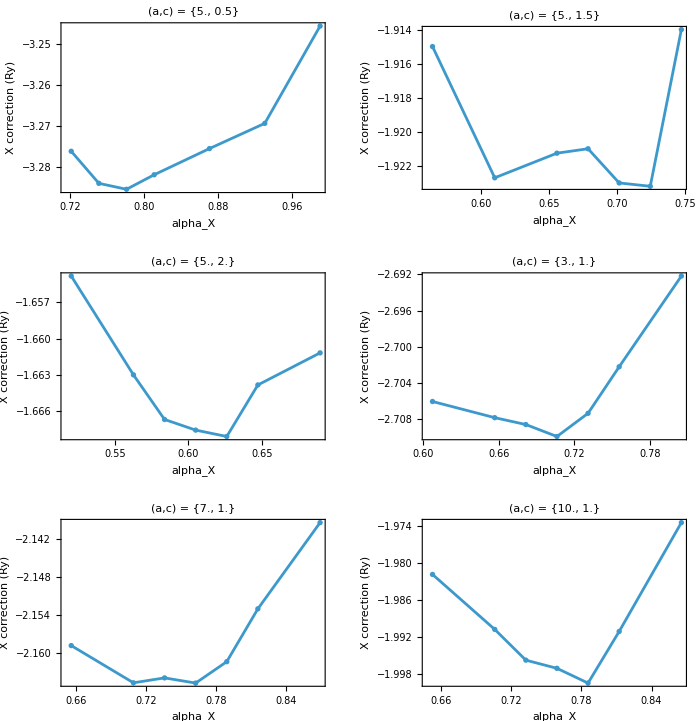

```mathematica
pscXPlot[]
```

## Biexciton initial stencils

This is the largest stage: the center and eight coordinate neighbors for each geometry, all at 1,000,000 MaxPoints. There are 54 candidates in the shared queue.

```mathematica
pscRunXXInitial[]
```

XX-initial-stencil: 54 requested; 54 missing; 0 reused.

XX-initial-stencil: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.3712859721644617|2.3827235819174315 on kernel 24; correction = -6.80637; remaining = 53

XX-initial-stencil: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.577484752352676|2.3827235819174315 on kernel 19; correction = -6.77622; remaining = 52

XX-initial-stencil: completed (5.|0.5) 0.8463776986063983|0.21332841922907436|2.577484752352676|2.3827235819174315 on kernel 21; correction = -6.73463; remaining = 51

XX-initial-stencil: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.577484752352676|2.1444512237256883 on kernel 26; correction = -6.72252; remaining = 50

XX-initial-stencil: completed (5.|0.5) 0.6650110489050273|0.21332841922907436|2.577484752352676|2.3827235819174315 on kernel 20; correction = -6.75045; remaining = 49

XX-initial-stencil: completed (5.|0.5) 0.7556943737557128|0.26666052403634294|2.577484752352676|2.3827235819174315 on kernel 23; correction = -6.73361; remaining = 48

XX-initial-stencil: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.78368353254089|2.3827235819174315 on kernel 25; correction = -6.64947; remaining = 47

XX-initial-stencil: completed (5.|0.5) 0.7556943737557128|0.15999631442180579|2.577484752352676|2.3827235819174315 on kernel 22; correction = -6.79275; remaining = 46

XX-initial-stencil: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.577484752352676|2.6209959401091747 on kernel 24; correction = -6.78075; remaining = 45

XX-initial-stencil: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|2.858881236727677|1.953280222542432 on kernel 19; correction = -3.99436; remaining = 44

XX-initial-stencil: completed (5.|1.5) 0.6807292611063978|0.004089211802105613|2.858881236727677|1.953280222542432 on kernel 26; correction = -3.98573; remaining = 43

XX-initial-stencil: completed (5.|1.5) 0.5348587051550269|0.004089211802105613|2.858881236727677|1.953280222542432 on kernel 21; correction = -3.95359; remaining = 42

XX-initial-stencil: completed (5.|1.5) 0.6077939831307123|0.001|2.858881236727677|1.953280222542432 on kernel 20; correction = -4.01052; remaining = 41

XX-initial-stencil: completed (5.|1.5) 0.6077939831307123|0.024089211802105614|2.858881236727677|1.953280222542432 on kernel 23; correction = -3.98511; remaining = 40

XX-initial-stencil: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|2.6301707377894625|1.953280222542432 on kernel 25; correction = -3.99879; remaining = 39

XX-initial-stencil: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|3.087591735665891|1.953280222542432 on kernel 22; correction = -3.97429; remaining = 38

XX-initial-stencil: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|2.858881236727677|1.7579522002881887 on kernel 24; correction = -3.98508; remaining = 37

XX-initial-stencil: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|2.858881236727677|2.1486082447966752 on kernel 19; correction = -3.96253; remaining = 36

XX-initial-stencil: completed (5.|2.) 0.5874814831307124|0.010584384475523713|3.0205999867276767|1.8743739725424318 on kernel 26; correction = -3.4461; remaining = 35

XX-initial-stencil: completed (5.|2.) 0.5169837051550269|0.010584384475523713|3.0205999867276767|1.8743739725424318 on kernel 21; correction = -3.4174; remaining = 34

XX-initial-stencil: completed (5.|2.) 0.5874814831307124|0.001|3.0205999867276767|1.8743739725424318 on kernel 23; correction = -3.46059; remaining = 33

XX-initial-stencil: completed (5.|2.) 0.6579792611063978|0.010584384475523713|3.0205999867276767|1.8743739725424318 on kernel 20; correction = -3.42674; remaining = 32

XX-initial-stencil: completed (5.|2.) 0.5874814831307124|0.030584384475523713|3.0205999867276767|1.8743739725424318 on kernel 25; correction = -3.44562; remaining = 31

XX-initial-stencil: completed (5.|2.) 0.5874814831307124|0.010584384475523713|2.7789519877894624|1.8743739725424318 on kernel 22; correction = -3.43083; remaining = 30

XX-initial-stencil: completed (5.|2.) 0.5874814831307124|0.010584384475523713|3.262247985665891|1.8743739725424318 on kernel 24; correction = -3.43124; remaining = 29

XX-initial-stencil: completed (5.|2.) 0.5874814831307124|0.010584384475523713|3.0205999867276767|1.6869365752881886 on kernel 19; correction = -3.45302; remaining = 28

XX-initial-stencil: completed (5.|2.) 0.5874814831307124|0.010584384475523713|3.0205999867276767|2.061811369796675 on kernel 26; correction = -3.39194; remaining = 27

XX-initial-stencil: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.2986903787924318 on kernel 21; correction = -5.64124; remaining = 26

XX-initial-stencil: completed (3.|1.) 0.7316980111063976|0.0633070356251368|2.5421820179776766|2.2986903787924318 on kernel 20; correction = -5.656; remaining = 25

XX-initial-stencil: completed (3.|1.) 0.5749055801550268|0.0633070356251368|2.5421820179776766|2.2986903787924318 on kernel 23; correction = -5.62842; remaining = 24

XX-initial-stencil: completed (3.|1.) 0.6533017956307122|0.0433070356251368|2.5421820179776766|2.2986903787924318 on kernel 25; correction = -5.64263; remaining = 23

XX-initial-stencil: completed (3.|1.) 0.6533017956307122|0.0833070356251368|2.5421820179776766|2.2986903787924318 on kernel 22; correction = -5.64412; remaining = 22

XX-initial-stencil: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.745556579415891|2.2986903787924318 on kernel 19; correction = -5.63039; remaining = 21

XX-initial-stencil: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.3388074565394623|2.2986903787924318 on kernel 24; correction = -5.65754; remaining = 20

XX-initial-stencil: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.0688213409131886 on kernel 26; correction = -5.63165; remaining = 19

XX-initial-stencil: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.528559416671675 on kernel 21; correction = -5.65798; remaining = 18

XX-initial-stencil: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 20; correction = -4.44638; remaining = 17

XX-initial-stencil: completed (7.|1.) 0.565280580155027|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 23; correction = -4.41636; remaining = 16

XX-initial-stencil: completed (7.|1.) 0.6423642956307125|0.03418019210545174|2.8304632679776756|1.8963466287924327 on kernel 22; correction = -4.43409; remaining = 15

XX-initial-stencil: completed (7.|1.) 0.719448011106398|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 25; correction = -4.44591; remaining = 14

XX-initial-stencil: completed (7.|1.) 0.6423642956307125|0.07418019210545175|2.8304632679776756|1.8963466287924327 on kernel 19; correction = -4.45018; remaining = 13

XX-initial-stencil: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.6040262065394617|1.8963466287924327 on kernel 24; correction = -4.46262; remaining = 12

XX-initial-stencil: completed (7.|1.) 0.6423642956307125|0.05418019210545175|3.0569003294158894|1.8963466287924327 on kernel 26; correction = -4.43919; remaining = 11

XX-initial-stencil: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|1.7067119659131893 on kernel 21; correction = -4.41196; remaining = 10

XX-initial-stencil: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|2.085981291671676 on kernel 20; correction = -4.44302; remaining = 9

XX-initial-stencil: completed (10.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 23; correction = -3.97841; remaining = 8

XX-initial-stencil: completed (10.|1.) 0.719448011106398|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 25; correction = -3.9994; remaining = 7

XX-initial-stencil: completed (10.|1.) 0.565280580155027|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 22; correction = -3.98929; remaining = 6

XX-initial-stencil: completed (10.|1.) 0.6423642956307125|0.03418019210545174|2.8304632679776756|1.8963466287924327 on kernel 19; correction = -4.02253; remaining = 5

XX-initial-stencil: completed (10.|1.) 0.6423642956307125|0.07418019210545175|2.8304632679776756|1.8963466287924327 on kernel 24; correction = -4.01443; remaining = 4

XX-initial-stencil: completed (10.|1.) 0.6423642956307125|0.05418019210545175|2.6040262065394617|1.8963466287924327 on kernel 26; correction = -3.98714; remaining = 3

XX-initial-stencil: completed (10.|1.) 0.6423642956307125|0.05418019210545175|3.0569003294158894|1.8963466287924327 on kernel 21; correction = -4.03123; remaining = 2

XX-initial-stencil: completed (10.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|1.7067119659131893 on kernel 20; correction = -3.99875; remaining = 1

XX-initial-stencil: completed (10.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|2.085981291671676 on kernel 23; correction = -3.93086; remaining = 0

{<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.21332841922907436|2.577484752352676|2.3827235819174315,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.213328,2.57748,2.38272},parameterKey→0.7556943737557128|0.21332841922907436|2.577484752352676|2.3827235819174315,norm→0.000565389,numeratorRy→-0.0038312,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.77622,roughCorrectionErrorRy→0.0236199,singleParticleRy→96.4876,totalRy→89.7114,elapsedSeconds→10066.5,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:49:02,integrals→{<|integral→normDenominator,seconds→588.528,value→0.000565389,hitMaxPoints→True,relativeErrorEstimate→0.00168738,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000565389 and 9.54028 10
     for the integral and error estimates.,messageIntegralEstimate→0.000565389,reportedErrorEstimate→9.54028×10^-7|>,<|integral→hamiltonianNumerator,seconds→9478.,value→-0.0038312,hitMaxPoints→True,relativeErrorEstimate→0.00305006,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0038312 and 0.0000116854
     for the integral and error estimates.,messageIntegralEstimate→-0.0038312,reportedErrorEstimate→0.0000116854|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.6650110489050273|0.21332841922907436|2.577484752352676|2.3827235819174315,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.665011,0.213328,2.57748,2.38272},parameterKey→0.6650110489050273|0.21332841922907436|2.577484752352676|2.3827235819174315,norm→0.00075247,numeratorRy→-0.00507951,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.75045,roughCorrectionErrorRy→0.0219142,singleParticleRy→96.4876,totalRy→89.7371,elapsedSeconds→10099.6,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:49:35,integrals→{<|integral→normDenominator,seconds→591.797,value→0.00075247,hitMaxPoints→True,relativeErrorEstimate→0.00156996,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00075247 and 1.18135 10
     for the integral and error estimates.,messageIntegralEstimate→0.00075247,reportedErrorEstimate→1.18135×10^-6|>,<|integral→hamiltonianNumerator,seconds→9507.78,value→-0.00507951,hitMaxPoints→True,relativeErrorEstimate→0.00284145,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00507951 and 0.0000144332
     for the integral and error estimates.,messageIntegralEstimate→-0.00507951,reportedErrorEstimate→0.0000144332|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.8463776986063983|0.21332841922907436|2.577484752352676|2.3827235819174315,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.846378,0.213328,2.57748,2.38272},parameterKey→0.8463776986063983|0.21332841922907436|2.577484752352676|2.3827235819174315,norm→0.000426992,numeratorRy→-0.00287563,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.73463,roughCorrectionErrorRy→0.0250238,singleParticleRy→96.4876,totalRy→89.7529,elapsedSeconds→10081.8,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:49:17,integrals→{<|integral→normDenominator,seconds→591.854,value→0.000426992,hitMaxPoints→True,relativeErrorEstimate→0.00179891,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000426992 and 7.68118 10
     for the integral and error estimates.,messageIntegralEstimate→0.000426992,reportedErrorEstimate→7.68118×10^-7|>,<|integral→hamiltonianNumerator,seconds→9489.93,value→-0.00287563,hitMaxPoints→True,relativeErrorEstimate→0.0032512,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00287563 and 9.34927 10
     for the integral and error estimates.,messageIntegralEstimate→-0.00287563,reportedErrorEstimate→9.34927×10^-6|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.15999631442180579|2.577484752352676|2.3827235819174315,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.159996,2.57748,2.38272},parameterKey→0.7556943737557128|0.15999631442180579|2.577484752352676|2.3827235819174315,norm→0.000681191,numeratorRy→-0.00462716,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.79275,roughCorrectionErrorRy→0.0227982,singleParticleRy→96.4876,totalRy→89.6948,elapsedSeconds→10147.2,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:50:23,integrals→{<|integral→normDenominator,seconds→595.899,value→0.000681191,hitMaxPoints→True,relativeErrorEstimate→0.00160413,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000681191 and 1.09272 10
     for the integral and error estimates.,messageIntegralEstimate→0.000681191,reportedErrorEstimate→1.09272×10^-6|>,<|integral→hamiltonianNumerator,seconds→9551.34,value→-0.00462716,hitMaxPoints→True,relativeErrorEstimate→0.00294809,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00462716 and 0.0000136413
     for the integral and error estimates.,messageIntegralEstimate→-0.00462716,reportedErrorEstimate→0.0000136413|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.26666052403634294|2.577484752352676|2.3827235819174315,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.266661,2.57748,2.38272},parameterKey→0.7556943737557128|0.26666052403634294|2.577484752352676|2.3827235819174315,norm→0.000469785,numeratorRy→-0.00316335,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.73361,roughCorrectionErrorRy→0.0243002,singleParticleRy→96.4876,totalRy→89.754,elapsedSeconds→10100.9,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:49:36,integrals→{<|integral→normDenominator,seconds→594.173,value→0.000469785,hitMaxPoints→True,relativeErrorEstimate→0.00174621,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000469785 and 8.20344 10
     for the integral and error estimates.,messageIntegralEstimate→0.000469785,reportedErrorEstimate→8.20344×10^-7|>,<|integral→hamiltonianNumerator,seconds→9506.72,value→-0.00316335,hitMaxPoints→True,relativeErrorEstimate→0.00315819,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00316335 and 9.99045 10
     for the integral and error estimates.,messageIntegralEstimate→-0.00316335,reportedErrorEstimate→9.99045×10^-6|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.21332841922907436|2.3712859721644617|2.3827235819174315,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.213328,2.37129,2.38272},parameterKey→0.7556943737557128|0.21332841922907436|2.3712859721644617|2.3827235819174315,norm→0.000583646,numeratorRy→-0.00397251,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.80637,roughCorrectionErrorRy→0.0242491,singleParticleRy→96.4876,totalRy→89.6812,elapsedSeconds→10052.8,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:48:48,integrals→{<|integral→normDenominator,seconds→590.205,value→0.000583646,hitMaxPoints→True,relativeErrorEstimate→0.00172654,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000583646 and 1.00769 10
     for the integral and error estimates.,messageIntegralEstimate→0.000583646,reportedErrorEstimate→1.00769×10^-6|>,<|integral→hamiltonianNumerator,seconds→9462.64,value→-0.00397251,hitMaxPoints→True,relativeErrorEstimate→0.00311639,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00397251 and 0.0000123799
     for the integral and error estimates.,messageIntegralEstimate→-0.00397251,reportedErrorEstimate→0.0000123799|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.21332841922907436|2.78368353254089|2.3827235819174315,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.213328,2.78368,2.38272},parameterKey→0.7556943737557128|0.21332841922907436|2.78368353254089|2.3827235819174315,norm→0.000557655,numeratorRy→-0.00370811,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.64947,roughCorrectionErrorRy→0.0227464,singleParticleRy→96.4876,totalRy→89.8381,elapsedSeconds→10134.6,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:50:10,integrals→{<|integral→normDenominator,seconds→594.692,value→0.000557655,hitMaxPoints→True,relativeErrorEstimate→0.0016416,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000557655 and 9.15444 10
     for the integral and error estimates.,messageIntegralEstimate→0.000557655,reportedErrorEstimate→9.15444×10^-7|>,<|integral→hamiltonianNumerator,seconds→9539.95,value→-0.00370811,hitMaxPoints→True,relativeErrorEstimate→0.00300115,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00370811 and 0.0000111286
     for the integral and error estimates.,messageIntegralEstimate→-0.00370811,reportedErrorEstimate→0.0000111286|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.21332841922907436|2.577484752352676|2.1444512237256883,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.213328,2.57748,2.14445},parameterKey→0.7556943737557128|0.21332841922907436|2.577484752352676|2.1444512237256883,norm→0.000921603,numeratorRy→-0.00619549,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.72252,roughCorrectionErrorRy→0.0223655,singleParticleRy→96.4876,totalRy→89.7651,elapsedSeconds→10084.5,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T14:01:15,completed→2026-08-01T16:49:20,integrals→{<|integral→normDenominator,seconds→589.654,value→0.000921603,hitMaxPoints→True,relativeErrorEstimate→0.00160274,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000921603 and 1.47709 10
     for the integral and error estimates.,messageIntegralEstimate→0.000921603,reportedErrorEstimate→1.47709×10^-6|>,<|integral→hamiltonianNumerator,seconds→9494.8,value→-0.00619549,hitMaxPoints→True,relativeErrorEstimate→0.00291544,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00619549 and 0.0000180626
     for the integral and error estimates.,messageIntegralEstimate→-0.00619549,reportedErrorEstimate→0.0000180626|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.21332841922907436|2.577484752352676|2.6209959401091747,stage→XX-initial-stencil,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.213328,2.57748,2.621},parameterKey→0.7556943737557128|0.21332841922907436|2.577484752352676|2.6209959401091747,norm→0.000354203,numeratorRy→-0.00240177,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.78075,roughCorrectionErrorRy→0.024585,singleParticleRy→96.4876,totalRy→89.7068,elapsedSeconds→10051.2,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:48:48,completed→2026-08-01T19:36:20,integrals→{<|integral→normDenominator,seconds→620.893,value→0.000354203,hitMaxPoints→True,relativeErrorEstimate→0.00175676,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -7
     integrand evaluations. NIntegrate obtained 0.000354203 and 6.2225 10
     for the integral and error estimates.,messageIntegralEstimate→0.000354203,reportedErrorEstimate→6.2225×10^-7|>,<|integral→hamiltonianNumerator,seconds→9430.35,value→-0.00240177,hitMaxPoints→True,relativeErrorEstimate→0.00317168,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00240177 and 7.61764 10
     for the integral and error estimates.,messageIntegralEstimate→-0.00240177,reportedErrorEstimate→7.61764×10^-6|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.004089211802105613|2.858881236727677|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.00408921,2.85888,1.95328},parameterKey→0.6077939831307123|0.004089211802105613|2.858881236727677|1.953280222542432,norm→0.00145962,numeratorRy→-0.00583024,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.99436,roughCorrectionErrorRy→0.0154794,singleParticleRy→12.0042,totalRy→8.0098,elapsedSeconds→10063.1,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:49:02,completed→2026-08-01T19:36:45,integrals→{<|integral→normDenominator,seconds→618.377,value→0.00145962,hitMaxPoints→True,relativeErrorEstimate→0.00203496,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00145962 and 2.97026 10
     for the integral and error estimates.,messageIntegralEstimate→0.00145962,reportedErrorEstimate→2.97026×10^-6|>,<|integral→hamiltonianNumerator,seconds→9444.73,value→-0.00583024,hitMaxPoints→True,relativeErrorEstimate→0.00329803,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00583024 and 0.0000192283
     for the integral and error estimates.,messageIntegralEstimate→-0.00583024,reportedErrorEstimate→0.0000192283|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.5348587051550269|0.004089211802105613|2.858881236727677|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.534859,0.00408921,2.85888,1.95328},parameterKey→0.5348587051550269|0.004089211802105613|2.858881236727677|1.953280222542432,norm→0.00212474,numeratorRy→-0.00840034,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.95359,roughCorrectionErrorRy→0.0142161,singleParticleRy→12.0042,totalRy→8.05057,elapsedSeconds→10075.8,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:49:17,completed→2026-08-01T19:37:13,integrals→{<|integral→normDenominator,seconds→621.663,value→0.00212474,hitMaxPoints→True,relativeErrorEstimate→0.00185458,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                        -6
     integrand evaluations. NIntegrate obtained 0.00212474 and 3.9405 10
     for the integral and error estimates.,messageIntegralEstimate→0.00212474,reportedErrorEstimate→3.9405×10^-6|>,<|integral→hamiltonianNumerator,seconds→9454.16,value→-0.00840034,hitMaxPoints→True,relativeErrorEstimate→0.00308058,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00840034 and 0.0000258779
     for the integral and error estimates.,messageIntegralEstimate→-0.00840034,reportedErrorEstimate→0.0000258779|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6807292611063978|0.004089211802105613|2.858881236727677|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.680729,0.00408921,2.85888,1.95328},parameterKey→0.6807292611063978|0.004089211802105613|2.858881236727677|1.953280222542432,norm→0.00101779,numeratorRy→-0.00405666,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.98573,roughCorrectionErrorRy→0.0167824,singleParticleRy→12.0042,totalRy→8.01843,elapsedSeconds→10069.2,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:49:20,completed→2026-08-01T19:37:09,integrals→{<|integral→normDenominator,seconds→621.502,value→0.00101779,hitMaxPoints→True,relativeErrorEstimate→0.00220818,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00101779 and 2.24747 10
     for the integral and error estimates.,messageIntegralEstimate→0.00101779,reportedErrorEstimate→2.24747×10^-6|>,<|integral→hamiltonianNumerator,seconds→9447.7,value→-0.00405666,hitMaxPoints→True,relativeErrorEstimate→0.00358514,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00405666 and 0.0000145437
     for the integral and error estimates.,messageIntegralEstimate→-0.00405666,reportedErrorEstimate→0.0000145437|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.001|2.858881236727677|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.001,2.85888,1.95328},parameterKey→0.6077939831307123|0.001|2.858881236727677|1.953280222542432,norm→0.00148348,numeratorRy→-0.0059495,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.01052,roughCorrectionErrorRy→0.0155468,singleParticleRy→12.0042,totalRy→7.99365,elapsedSeconds→10102.3,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:49:35,completed→2026-08-01T19:37:57,integrals→{<|integral→normDenominator,seconds→623.763,value→0.00148348,hitMaxPoints→True,relativeErrorEstimate→0.00202102,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00148348 and 2.99814 10
     for the integral and error estimates.,messageIntegralEstimate→0.00148348,reportedErrorEstimate→2.99814×10^-6|>,<|integral→hamiltonianNumerator,seconds→9478.54,value→-0.0059495,hitMaxPoints→True,relativeErrorEstimate→0.00330799,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0059495 and 0.0000196809
     for the integral and error estimates.,messageIntegralEstimate→-0.0059495,reportedErrorEstimate→0.0000196809|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.024089211802105614|2.858881236727677|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.0240892,2.85888,1.95328},parameterKey→0.6077939831307123|0.024089211802105614|2.858881236727677|1.953280222542432,norm→0.00129681,numeratorRy→-0.00516794,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.98511,roughCorrectionErrorRy→0.0157172,singleParticleRy→12.0042,totalRy→8.01906,elapsedSeconds→10103.5,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:49:36,completed→2026-08-01T19:38:00,integrals→{<|integral→normDenominator,seconds→622.896,value→0.00129681,hitMaxPoints→True,relativeErrorEstimate→0.00208271,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00129681 and 2.70089 10
     for the integral and error estimates.,messageIntegralEstimate→0.00129681,reportedErrorEstimate→2.70089×10^-6|>,<|integral→hamiltonianNumerator,seconds→9480.57,value→-0.00516794,hitMaxPoints→True,relativeErrorEstimate→0.00334923,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00516794 and 0.0000173086
     for the integral and error estimates.,messageIntegralEstimate→-0.00516794,reportedErrorEstimate→0.0000173086|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.004089211802105613|2.6301707377894625|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.00408921,2.63017,1.95328},parameterKey→0.6077939831307123|0.004089211802105613|2.6301707377894625|1.953280222542432,norm→0.00124231,numeratorRy→-0.00496772,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.99879,roughCorrectionErrorRy→0.0160195,singleParticleRy→12.0042,totalRy→8.00537,elapsedSeconds→10138.,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:50:10,completed→2026-08-01T19:39:08,integrals→{<|integral→normDenominator,seconds→621.257,value→0.00124231,hitMaxPoints→True,relativeErrorEstimate→0.00210197,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00124231 and 2.61129 10
     for the integral and error estimates.,messageIntegralEstimate→0.00124231,reportedErrorEstimate→2.61129×10^-6|>,<|integral→hamiltonianNumerator,seconds→9516.7,value→-0.00496772,hitMaxPoints→True,relativeErrorEstimate→0.00341033,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00496772 and 0.0000169416
     for the integral and error estimates.,messageIntegralEstimate→-0.00496772,reportedErrorEstimate→0.0000169416|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.004089211802105613|3.087591735665891|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.00408921,3.08759,1.95328},parameterKey→0.6077939831307123|0.004089211802105613|3.087591735665891|1.953280222542432,norm→0.00174819,numeratorRy→-0.00694784,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.97429,roughCorrectionErrorRy→0.0151091,singleParticleRy→12.0042,totalRy→8.02987,elapsedSeconds→10146.8,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:50:23,completed→2026-08-01T19:39:30,integrals→{<|integral→normDenominator,seconds→623.228,value→0.00174819,hitMaxPoints→True,relativeErrorEstimate→0.00197055,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00174819 and 3.44491 10
     for the integral and error estimates.,messageIntegralEstimate→0.00174819,reportedErrorEstimate→3.44491×10^-6|>,<|integral→hamiltonianNumerator,seconds→9523.59,value→-0.00694784,hitMaxPoints→True,relativeErrorEstimate→0.00325114,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00694784 and 0.0000225884
     for the integral and error estimates.,messageIntegralEstimate→-0.00694784,reportedErrorEstimate→0.0000225884|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.004089211802105613|2.858881236727677|1.7579522002881887,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.00408921,2.85888,1.75795},parameterKey→0.6077939831307123|0.004089211802105613|2.858881236727677|1.7579522002881887,norm→0.00270813,numeratorRy→-0.0107921,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.98508,roughCorrectionErrorRy→0.0147155,singleParticleRy→12.0042,totalRy→8.01909,elapsedSeconds→10046.8,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:36:20,completed→2026-08-01T22:23:46,integrals→{<|integral→normDenominator,seconds→613.854,value→0.00270813,hitMaxPoints→True,relativeErrorEstimate→0.00191619,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00270813 and 5.18931 10
     for the integral and error estimates.,messageIntegralEstimate→0.00270813,reportedErrorEstimate→5.18931×10^-6|>,<|integral→hamiltonianNumerator,seconds→9432.96,value→-0.0107921,hitMaxPoints→True,relativeErrorEstimate→0.00315657,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0107921 and 0.0000340661
     for the integral and error estimates.,messageIntegralEstimate→-0.0107921,reportedErrorEstimate→0.0000340661|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.004089211802105613|2.858881236727677|2.1486082447966752,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.00408921,2.85888,2.14861},parameterKey→0.6077939831307123|0.004089211802105613|2.858881236727677|2.1486082447966752,norm→0.000815115,numeratorRy→-0.00322992,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.96253,roughCorrectionErrorRy→0.0162096,singleParticleRy→12.0042,totalRy→8.04164,elapsedSeconds→10044.5,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:36:45,completed→2026-08-01T22:24:10,integrals→{<|integral→normDenominator,seconds→612.723,value→0.000815115,hitMaxPoints→True,relativeErrorEstimate→0.00215331,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.000815115 and 1.7552 10
     for the integral and error estimates.,messageIntegralEstimate→0.000815115,reportedErrorEstimate→1.7552×10^-6|>,<|integral→hamiltonianNumerator,seconds→9431.82,value→-0.00322992,hitMaxPoints→True,relativeErrorEstimate→0.00347811,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00322992 and 0.000011234
     for the integral and error estimates.,messageIntegralEstimate→-0.00322992,reportedErrorEstimate→0.000011234|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.010584384475523713|3.0205999867276767|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0105844,3.0206,1.87437},parameterKey→0.5874814831307124|0.010584384475523713|3.0205999867276767|1.8743739725424318,norm→0.00134081,numeratorRy→-0.00462057,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.4461,roughCorrectionErrorRy→0.0147867,singleParticleRy→7.11328,totalRy→3.66717,elapsedSeconds→10066.,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:37:09,completed→2026-08-01T22:24:55,integrals→{<|integral→normDenominator,seconds→616.503,value→0.00134081,hitMaxPoints→True,relativeErrorEstimate→0.00229474,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00134081 and 3.07681 10
     for the integral and error estimates.,messageIntegralEstimate→0.00134081,reportedErrorEstimate→3.07681×10^-6|>,<|integral→hamiltonianNumerator,seconds→9449.49,value→-0.00462057,hitMaxPoints→True,relativeErrorEstimate→0.00362568,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00462057 and 0.0000167527
     for the integral and error estimates.,messageIntegralEstimate→-0.00462057,reportedErrorEstimate→0.0000167527|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5169837051550269|0.010584384475523713|3.0205999867276767|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.516984,0.0105844,3.0206,1.87437},parameterKey→0.5169837051550269|0.010584384475523713|3.0205999867276767|1.8743739725424318,norm→0.00200974,numeratorRy→-0.00686809,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.4174,roughCorrectionErrorRy→0.0134816,singleParticleRy→7.11328,totalRy→3.69588,elapsedSeconds→10088.1,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:37:13,completed→2026-08-01T22:25:21,integrals→{<|integral→normDenominator,seconds→616.547,value→0.00200974,hitMaxPoints→True,relativeErrorEstimate→0.00209748,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                        -6
     integrand evaluations. NIntegrate obtained 0.00200974 and 4.2154 10
     for the integral and error estimates.,messageIntegralEstimate→0.00200974,reportedErrorEstimate→4.2154×10^-6|>,<|integral→hamiltonianNumerator,seconds→9471.52,value→-0.00686809,hitMaxPoints→True,relativeErrorEstimate→0.00334119,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00686809 and 0.0000229476
     for the integral and error estimates.,messageIntegralEstimate→-0.00686809,reportedErrorEstimate→0.0000229476|>}|>,<|candidateKey→5.|2.::XX::1000000::0.6579792611063978|0.010584384475523713|3.0205999867276767|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.657979,0.0105844,3.0206,1.87437},parameterKey→0.6579792611063978|0.010584384475523713|3.0205999867276767|1.8743739725424318,norm→0.000907033,numeratorRy→-0.00310816,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.42674,roughCorrectionErrorRy→0.0158438,singleParticleRy→7.11328,totalRy→3.68654,elapsedSeconds→10099.2,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:37:57,completed→2026-08-01T22:26:17,integrals→{<|integral→normDenominator,seconds→618.859,value→0.000907033,hitMaxPoints→True,relativeErrorEstimate→0.00249462,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.000907033 and 2.2627 10
     for the integral and error estimates.,messageIntegralEstimate→0.000907033,reportedErrorEstimate→2.2627×10^-6|>,<|integral→hamiltonianNumerator,seconds→9480.32,value→-0.00310816,hitMaxPoints→True,relativeErrorEstimate→0.00389288,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00310816 and 0.0000120997
     for the integral and error estimates.,messageIntegralEstimate→-0.00310816,reportedErrorEstimate→0.0000120997|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.001|3.0205999867276767|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.001,3.0206,1.87437},parameterKey→0.5874814831307124|0.001|3.0205999867276767|1.8743739725424318,norm→0.00142863,numeratorRy→-0.00494392,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.46059,roughCorrectionErrorRy→0.0146485,singleParticleRy→7.11328,totalRy→3.65269,elapsedSeconds→10087.2,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:38:00,completed→2026-08-01T22:26:07,integrals→{<|integral→normDenominator,seconds→618.143,value→0.00142863,hitMaxPoints→True,relativeErrorEstimate→0.00227106,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00142863 and 3.24452 10
     for the integral and error estimates.,messageIntegralEstimate→0.00142863,reportedErrorEstimate→3.24452×10^-6|>,<|integral→hamiltonianNumerator,seconds→9469.05,value→-0.00494392,hitMaxPoints→True,relativeErrorEstimate→0.00357213,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00494392 and 0.0000176603
     for the integral and error estimates.,messageIntegralEstimate→-0.00494392,reportedErrorEstimate→0.0000176603|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.030584384475523713|3.0205999867276767|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0305844,3.0206,1.87437},parameterKey→0.5874814831307124|0.030584384475523713|3.0205999867276767|1.8743739725424318,norm→0.00117165,numeratorRy→-0.00403707,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.44562,roughCorrectionErrorRy→0.0150492,singleParticleRy→7.11328,totalRy→3.66766,elapsedSeconds→10140.2,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:39:08,completed→2026-08-01T22:28:08,integrals→{<|integral→normDenominator,seconds→618.458,value→0.00117165,hitMaxPoints→True,relativeErrorEstimate→0.00234487,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00117165 and 2.74738 10
     for the integral and error estimates.,messageIntegralEstimate→0.00117165,reportedErrorEstimate→2.74738×10^-6|>,<|integral→hamiltonianNumerator,seconds→9521.69,value→-0.00403707,hitMaxPoints→True,relativeErrorEstimate→0.0036848,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00403707 and 0.0000148758
     for the integral and error estimates.,messageIntegralEstimate→-0.00403707,reportedErrorEstimate→0.0000148758|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.010584384475523713|2.7789519877894624|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0105844,2.77895,1.87437},parameterKey→0.5874814831307124|0.010584384475523713|2.7789519877894624|1.8743739725424318,norm→0.00107346,numeratorRy→-0.00368285,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.43083,roughCorrectionErrorRy→0.0153426,singleParticleRy→7.11328,totalRy→3.68244,elapsedSeconds→10121.7,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:39:30,completed→2026-08-01T22:28:11,integrals→{<|integral→normDenominator,seconds→621.368,value→0.00107346,hitMaxPoints→True,relativeErrorEstimate→0.00237174,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00107346 and 2.54596 10
     for the integral and error estimates.,messageIntegralEstimate→0.00107346,reportedErrorEstimate→2.54596×10^-6|>,<|integral→hamiltonianNumerator,seconds→9500.37,value→-0.00368285,hitMaxPoints→True,relativeErrorEstimate→0.00379122,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00368285 and 0.0000139625
     for the integral and error estimates.,messageIntegralEstimate→-0.00368285,reportedErrorEstimate→0.0000139625|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.010584384475523713|3.262247985665891|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0105844,3.26225,1.87437},parameterKey→0.5874814831307124|0.010584384475523713|3.262247985665891|1.8743739725424318,norm→0.00171451,numeratorRy→-0.0058829,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.43124,roughCorrectionErrorRy→0.0143074,singleParticleRy→7.11328,totalRy→3.68204,elapsedSeconds→10070.5,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:23:46,completed→2026-08-02T01:11:37,integrals→{<|integral→normDenominator,seconds→618.608,value→0.00171451,hitMaxPoints→True,relativeErrorEstimate→0.00222231,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00171451 and 3.81017 10
     for the integral and error estimates.,messageIntegralEstimate→0.00171451,reportedErrorEstimate→3.81017×10^-6|>,<|integral→hamiltonianNumerator,seconds→9451.9,value→-0.0058829,hitMaxPoints→True,relativeErrorEstimate→0.00352819,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0058829 and 0.000020756
     for the integral and error estimates.,messageIntegralEstimate→-0.0058829,reportedErrorEstimate→0.000020756|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.010584384475523713|3.0205999867276767|1.6869365752881886,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0105844,3.0206,1.68694},parameterKey→0.5874814831307124|0.010584384475523713|3.0205999867276767|1.6869365752881886,norm→0.00259833,numeratorRy→-0.00897209,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.45302,roughCorrectionErrorRy→0.0141483,singleParticleRy→7.11328,totalRy→3.66025,elapsedSeconds→10056.1,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:24:10,completed→2026-08-02T01:11:46,integrals→{<|integral→normDenominator,seconds→613.33,value→0.00259833,hitMaxPoints→True,relativeErrorEstimate→0.00216814,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00259833 and 5.63355 10
     for the integral and error estimates.,messageIntegralEstimate→0.00259833,reportedErrorEstimate→5.63355×10^-6|>,<|integral→hamiltonianNumerator,seconds→9442.72,value→-0.00897209,hitMaxPoints→True,relativeErrorEstimate→0.00347671,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00897209 and 0.0000311934
     for the integral and error estimates.,messageIntegralEstimate→-0.00897209,reportedErrorEstimate→0.0000311934|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.010584384475523713|3.0205999867276767|2.061811369796675,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0105844,3.0206,2.06181},parameterKey→0.5874814831307124|0.010584384475523713|3.0205999867276767|2.061811369796675,norm→0.00072066,numeratorRy→-0.00244443,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.39194,roughCorrectionErrorRy→0.0154689,singleParticleRy→7.11328,totalRy→3.72134,elapsedSeconds→10070.2,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:24:55,completed→2026-08-02T01:12:45,integrals→{<|integral→normDenominator,seconds→616.383,value→0.00072066,hitMaxPoints→True,relativeErrorEstimate→0.00243095,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00072066 and 1.75189 10
     for the integral and error estimates.,messageIntegralEstimate→0.00072066,reportedErrorEstimate→1.75189×10^-6|>,<|integral→hamiltonianNumerator,seconds→9453.83,value→-0.00244443,hitMaxPoints→True,relativeErrorEstimate→0.00385857,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00244443 and 9.43202 10
     for the integral and error estimates.,messageIntegralEstimate→-0.00244443,reportedErrorEstimate→9.43202×10^-6|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.5421820179776766|2.2986903787924318,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.54218,2.29869},parameterKey→0.6533017956307122|0.0633070356251368|2.5421820179776766|2.2986903787924318,norm→0.00124188,numeratorRy→-0.00700573,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.64124,roughCorrectionErrorRy→0.0168886,singleParticleRy→27.4906,totalRy→21.8494,elapsedSeconds→10084.6,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:25:21,completed→2026-08-02T01:13:26,integrals→{<|integral→normDenominator,seconds→615.97,value→0.00124188,hitMaxPoints→True,relativeErrorEstimate→0.00145774,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00124188 and 1.81033 10
     for the integral and error estimates.,messageIntegralEstimate→0.00124188,reportedErrorEstimate→1.81033×10^-6|>,<|integral→hamiltonianNumerator,seconds→9468.61,value→-0.00700573,hitMaxPoints→True,relativeErrorEstimate→0.00261489,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00700573 and 0.0000183192
     for the integral and error estimates.,messageIntegralEstimate→-0.00700573,reportedErrorEstimate→0.0000183192|>}|>,<|candidateKey→3.|1.::XX::1000000::0.5749055801550268|0.0633070356251368|2.5421820179776766|2.2986903787924318,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.574906,0.063307,2.54218,2.29869},parameterKey→0.5749055801550268|0.0633070356251368|2.5421820179776766|2.2986903787924318,norm→0.00165813,numeratorRy→-0.00933264,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.62842,roughCorrectionErrorRy→0.0159486,singleParticleRy→27.4906,totalRy→21.8622,elapsedSeconds→10119.5,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:26:07,completed→2026-08-02T01:14:47,integrals→{<|integral→normDenominator,seconds→617.065,value→0.00165813,hitMaxPoints→True,relativeErrorEstimate→0.00136123,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00165813 and 2.25709 10
     for the integral and error estimates.,messageIntegralEstimate→0.00165813,reportedErrorEstimate→2.25709×10^-6|>,<|integral→hamiltonianNumerator,seconds→9502.41,value→-0.00933264,hitMaxPoints→True,relativeErrorEstimate→0.0024852,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00933264 and 0.0000231935
     for the integral and error estimates.,messageIntegralEstimate→-0.00933264,reportedErrorEstimate→0.0000231935|>}|>,<|candidateKey→3.|1.::XX::1000000::0.7316980111063976|0.0633070356251368|2.5421820179776766|2.2986903787924318,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.731698,0.063307,2.54218,2.29869},parameterKey→0.7316980111063976|0.0633070356251368|2.5421820179776766|2.2986903787924318,norm→0.000936206,numeratorRy→-0.00529518,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.656,roughCorrectionErrorRy→0.0181537,singleParticleRy→27.4906,totalRy→21.8346,elapsedSeconds→10109.8,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:26:17,completed→2026-08-02T01:14:46,integrals→{<|integral→normDenominator,seconds→615.689,value→0.000936206,hitMaxPoints→True,relativeErrorEstimate→0.00155675,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000936206 and 1.45744 10
     for the integral and error estimates.,messageIntegralEstimate→0.000936206,reportedErrorEstimate→1.45744×10^-6|>,<|integral→hamiltonianNumerator,seconds→9494.1,value→-0.00529518,hitMaxPoints→True,relativeErrorEstimate→0.00280684,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00529518 and 0.0000148627
     for the integral and error estimates.,messageIntegralEstimate→-0.00529518,reportedErrorEstimate→0.0000148627|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0433070356251368|2.5421820179776766|2.2986903787924318,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.043307,2.54218,2.29869},parameterKey→0.6533017956307122|0.0433070356251368|2.5421820179776766|2.2986903787924318,norm→0.00134761,numeratorRy→-0.00760407,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.64263,roughCorrectionErrorRy→0.0167671,singleParticleRy→27.4906,totalRy→21.848,elapsedSeconds→10158.2,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:28:08,completed→2026-08-02T01:17:27,integrals→{<|integral→normDenominator,seconds→617.008,value→0.00134761,hitMaxPoints→True,relativeErrorEstimate→0.00143354,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00134761 and 1.93186 10
     for the integral and error estimates.,messageIntegralEstimate→0.00134761,reportedErrorEstimate→1.93186×10^-6|>,<|integral→hamiltonianNumerator,seconds→9541.21,value→-0.00760407,hitMaxPoints→True,relativeErrorEstimate→0.00260284,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00760407 and 0.0000197922
     for the integral and error estimates.,messageIntegralEstimate→-0.00760407,reportedErrorEstimate→0.0000197922|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0833070356251368|2.5421820179776766|2.2986903787924318,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.083307,2.54218,2.29869},parameterKey→0.6533017956307122|0.0833070356251368|2.5421820179776766|2.2986903787924318,norm→0.00114412,numeratorRy→-0.00645754,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.64412,roughCorrectionErrorRy→0.0171578,singleParticleRy→27.4906,totalRy→21.8465,elapsedSeconds→10168.6,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T22:28:11,completed→2026-08-02T01:17:40,integrals→{<|integral→normDenominator,seconds→618.537,value→0.00114412,hitMaxPoints→True,relativeErrorEstimate→0.0014857,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00114412 and 1.69982 10
     for the integral and error estimates.,messageIntegralEstimate→0.00114412,reportedErrorEstimate→1.69982×10^-6|>,<|integral→hamiltonianNumerator,seconds→9550.02,value→-0.00645754,hitMaxPoints→True,relativeErrorEstimate→0.00265215,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00645754 and 0.0000171264
     for the integral and error estimates.,messageIntegralEstimate→-0.00645754,reportedErrorEstimate→0.0000171264|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.3388074565394623|2.2986903787924318,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.33881,2.29869},parameterKey→0.6533017956307122|0.0633070356251368|2.3388074565394623|2.2986903787924318,norm→0.00123764,numeratorRy→-0.00700198,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.65754,roughCorrectionErrorRy→0.0175246,singleParticleRy→27.4906,totalRy→21.8331,elapsedSeconds→10413.1,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:11:37,completed→2026-08-02T04:05:10,integrals→{<|integral→normDenominator,seconds→619.18,value→0.00123764,hitMaxPoints→True,relativeErrorEstimate→0.00151116,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00123764 and 1.87027 10
     for the integral and error estimates.,messageIntegralEstimate→0.00123764,reportedErrorEstimate→1.87027×10^-6|>,<|integral→hamiltonianNumerator,seconds→9793.9,value→-0.00700198,hitMaxPoints→True,relativeErrorEstimate→0.00270394,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00700198 and 0.0000189329
     for the integral and error estimates.,messageIntegralEstimate→-0.00700198,reportedErrorEstimate→0.0000189329|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.745556579415891|2.2986903787924318,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.74556,2.29869},parameterKey→0.6533017956307122|0.0633070356251368|2.745556579415891|2.2986903787924318,norm→0.00126893,numeratorRy→-0.00714456,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.63039,roughCorrectionErrorRy→0.0166917,singleParticleRy→27.4906,totalRy→21.8602,elapsedSeconds→10380.8,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:11:46,completed→2026-08-02T04:04:47,integrals→{<|integral→normDenominator,seconds→615.893,value→0.00126893,hitMaxPoints→True,relativeErrorEstimate→0.00143598,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00126893 and 1.82216 10
     for the integral and error estimates.,messageIntegralEstimate→0.00126893,reportedErrorEstimate→1.82216×10^-6|>,<|integral→hamiltonianNumerator,seconds→9764.89,value→-0.00714456,hitMaxPoints→True,relativeErrorEstimate→0.00259358,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00714456 and 0.00001853
     for the integral and error estimates.,messageIntegralEstimate→-0.00714456,reportedErrorEstimate→0.00001853|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.5421820179776766|2.0688213409131886,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.54218,2.06882},parameterKey→0.6533017956307122|0.0633070356251368|2.5421820179776766|2.0688213409131886,norm→0.00208139,numeratorRy→-0.0117216,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.63165,roughCorrectionErrorRy→0.0163296,singleParticleRy→27.4906,totalRy→21.859,elapsedSeconds→10405.8,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:12:45,completed→2026-08-02T04:06:11,integrals→{<|integral→normDenominator,seconds→618.767,value→0.00208139,hitMaxPoints→True,relativeErrorEstimate→0.00139768,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00208139 and 2.90912 10
     for the integral and error estimates.,messageIntegralEstimate→0.00208139,reportedErrorEstimate→2.90912×10^-6|>,<|integral→hamiltonianNumerator,seconds→9787.06,value→-0.0117216,hitMaxPoints→True,relativeErrorEstimate→0.00254052,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0117216 and 0.000029779
     for the integral and error estimates.,messageIntegralEstimate→-0.0117216,reportedErrorEstimate→0.000029779|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.5421820179776766|2.528559416671675,stage→XX-initial-stencil,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.54218,2.52856},parameterKey→0.6533017956307122|0.0633070356251368|2.5421820179776766|2.528559416671675,norm→0.000760513,numeratorRy→-0.00430297,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.65798,roughCorrectionErrorRy→0.0179353,singleParticleRy→27.4906,totalRy→21.8326,elapsedSeconds→10405.8,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:13:26,completed→2026-08-02T04:06:52,integrals→{<|integral→normDenominator,seconds→617.923,value→0.000760513,hitMaxPoints→True,relativeErrorEstimate→0.00154655,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000760513 and 1.17617 10
     for the integral and error estimates.,messageIntegralEstimate→0.000760513,reportedErrorEstimate→1.17617×10^-6|>,<|integral→hamiltonianNumerator,seconds→9787.87,value→-0.00430297,hitMaxPoints→True,relativeErrorEstimate→0.00276704,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00430297 and 0.0000119065
     for the integral and error estimates.,messageIntegralEstimate→-0.00430297,reportedErrorEstimate→0.0000119065|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.83046,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327,norm→0.0012826,numeratorRy→-0.0057029,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.44638,roughCorrectionErrorRy→0.0182044,singleParticleRy→24.7406,totalRy→20.2943,elapsedSeconds→10406.2,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:14:46,completed→2026-08-02T04:08:13,integrals→{<|integral→normDenominator,seconds→620.745,value→0.0012826,hitMaxPoints→True,relativeErrorEstimate→0.00212304,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                      -6
     integrand evaluations. NIntegrate obtained 0.0012826 and 2.723 10
     for the integral and error estimates.,messageIntegralEstimate→0.0012826,reportedErrorEstimate→2.723×10^-6|>,<|integral→hamiltonianNumerator,seconds→9785.46,value→-0.0057029,hitMaxPoints→True,relativeErrorEstimate→0.00350076,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0057029 and 0.0000199645
     for the integral and error estimates.,messageIntegralEstimate→-0.0057029,reportedErrorEstimate→0.0000199645|>}|>,<|candidateKey→7.|1.::XX::1000000::0.565280580155027|0.05418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.565281,0.0541802,2.83046,1.89635},parameterKey→0.565280580155027|0.05418019210545175|2.8304632679776756|1.8963466287924327,norm→0.00185472,numeratorRy→-0.00819111,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.41636,roughCorrectionErrorRy→0.0167383,singleParticleRy→24.7406,totalRy→20.3243,elapsedSeconds→10431.3,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:14:47,completed→2026-08-02T04:08:38,integrals→{<|integral→normDenominator,seconds→622.413,value→0.00185472,hitMaxPoints→True,relativeErrorEstimate→0.00196508,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00185472 and 3.64467 10
     for the integral and error estimates.,messageIntegralEstimate→0.00185472,reportedErrorEstimate→3.64467×10^-6|>,<|integral→hamiltonianNumerator,seconds→9808.88,value→-0.00819111,hitMaxPoints→True,relativeErrorEstimate→0.00324083,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00819111 and 0.000026546
     for the integral and error estimates.,messageIntegralEstimate→-0.00819111,reportedErrorEstimate→0.000026546|>}|>,<|candidateKey→7.|1.::XX::1000000::0.719448011106398|0.05418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.719448,0.0541802,2.83046,1.89635},parameterKey→0.719448011106398|0.05418019210545175|2.8304632679776756|1.8963466287924327,norm→0.000901169,numeratorRy→-0.00400652,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.44591,roughCorrectionErrorRy→0.0195818,singleParticleRy→24.7406,totalRy→20.2947,elapsedSeconds→10467.4,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:17:27,completed→2026-08-02T04:11:54,integrals→{<|integral→normDenominator,seconds→620.726,value→0.000901169,hitMaxPoints→True,relativeErrorEstimate→0.00231398,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000901169 and 2.08529 10
     for the integral and error estimates.,messageIntegralEstimate→0.000901169,reportedErrorEstimate→2.08529×10^-6|>,<|integral→hamiltonianNumerator,seconds→9846.64,value→-0.00400652,hitMaxPoints→True,relativeErrorEstimate→0.00374762,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00400652 and 0.0000150149
     for the integral and error estimates.,messageIntegralEstimate→-0.00400652,reportedErrorEstimate→0.0000150149|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.03418019210545174|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0341802,2.83046,1.89635},parameterKey→0.6423642956307125|0.03418019210545174|2.8304632679776756|1.8963466287924327,norm→0.00143528,numeratorRy→-0.00636417,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.43409,roughCorrectionErrorRy→0.017863,singleParticleRy→24.7406,totalRy→20.3066,elapsedSeconds→10450.8,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T01:17:40,completed→2026-08-02T04:11:51,integrals→{<|integral→normDenominator,seconds→623.4,value→0.00143528,hitMaxPoints→True,relativeErrorEstimate→0.00208737,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00143528 and 2.99597 10
     for the integral and error estimates.,messageIntegralEstimate→0.00143528,reportedErrorEstimate→2.99597×10^-6|>,<|integral→hamiltonianNumerator,seconds→9827.37,value→-0.00636417,hitMaxPoints→True,relativeErrorEstimate→0.00344562,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00636417 and 0.0000219285
     for the integral and error estimates.,messageIntegralEstimate→-0.00636417,reportedErrorEstimate→0.0000219285|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.07418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0741802,2.83046,1.89635},parameterKey→0.6423642956307125|0.07418019210545175|2.8304632679776756|1.8963466287924327,norm→0.0011468,numeratorRy→-0.00510345,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.45018,roughCorrectionErrorRy→0.0185605,singleParticleRy→24.7406,totalRy→20.2905,elapsedSeconds→10110.4,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:04:47,completed→2026-08-02T06:53:17,integrals→{<|integral→normDenominator,seconds→618.818,value→0.0011468,hitMaxPoints→True,relativeErrorEstimate→0.00217478,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                        -6
     integrand evaluations. NIntegrate obtained 0.0011468 and 2.49403 10
     for the integral and error estimates.,messageIntegralEstimate→0.0011468,reportedErrorEstimate→2.49403×10^-6|>,<|integral→hamiltonianNumerator,seconds→9491.57,value→-0.00510345,hitMaxPoints→True,relativeErrorEstimate→0.00355885,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00510345 and 0.0000181624
     for the integral and error estimates.,messageIntegralEstimate→-0.00510345,reportedErrorEstimate→0.0000181624|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.6040262065394617|1.8963466287924327,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.60403,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|2.6040262065394617|1.8963466287924327,norm→0.0011074,numeratorRy→-0.00494192,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.46262,roughCorrectionErrorRy→0.0187001,singleParticleRy→24.7406,totalRy→20.278,elapsedSeconds→10113.8,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:05:10,completed→2026-08-02T06:53:44,integrals→{<|integral→normDenominator,seconds→618.892,value→0.0011074,hitMaxPoints→True,relativeErrorEstimate→0.00218567,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                        -6
     integrand evaluations. NIntegrate obtained 0.0011074 and 2.42042 10
     for the integral and error estimates.,messageIntegralEstimate→0.0011074,reportedErrorEstimate→2.42042×10^-6|>,<|integral→hamiltonianNumerator,seconds→9494.94,value→-0.00494192,hitMaxPoints→True,relativeErrorEstimate→0.00357523,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00494192 and 0.0000176685
     for the integral and error estimates.,messageIntegralEstimate→-0.00494192,reportedErrorEstimate→0.0000176685|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|3.0569003294158894|1.8963466287924327,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,3.0569,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|3.0569003294158894|1.8963466287924327,norm→0.00151791,numeratorRy→-0.00673829,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.43919,roughCorrectionErrorRy→0.0175979,singleParticleRy→24.7406,totalRy→20.3014,elapsedSeconds→10155.9,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:06:11,completed→2026-08-02T06:55:27,integrals→{<|integral→normDenominator,seconds→621.432,value→0.00151791,hitMaxPoints→True,relativeErrorEstimate→0.00206682,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00151791 and 3.13724 10
     for the integral and error estimates.,messageIntegralEstimate→0.00151791,reportedErrorEstimate→3.13724×10^-6|>,<|integral→hamiltonianNumerator,seconds→9534.45,value→-0.00673829,hitMaxPoints→True,relativeErrorEstimate→0.00338279,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00673829 and 0.0000227942
     for the integral and error estimates.,messageIntegralEstimate→-0.00673829,reportedErrorEstimate→0.0000227942|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.8304632679776756|1.7067119659131893,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.83046,1.70671},parameterKey→0.6423642956307125|0.05418019210545175|2.8304632679776756|1.7067119659131893,norm→0.00230532,numeratorRy→-0.010171,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.41196,roughCorrectionErrorRy→0.0171582,singleParticleRy→24.7406,totalRy→20.3287,elapsedSeconds→10141.8,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:06:52,completed→2026-08-02T06:55:53,integrals→{<|integral→normDenominator,seconds→619.978,value→0.00230532,hitMaxPoints→True,relativeErrorEstimate→0.00200826,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00230532 and 4.62968 10
     for the integral and error estimates.,messageIntegralEstimate→0.00230532,reportedErrorEstimate→4.62968×10^-6|>,<|integral→hamiltonianNumerator,seconds→9521.86,value→-0.010171,hitMaxPoints→True,relativeErrorEstimate→0.00333038,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.010171 and 0.0000338732
     for the integral and error estimates.,messageIntegralEstimate→-0.010171,reportedErrorEstimate→0.0000338732|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.8304632679776756|2.085981291671676,stage→XX-initial-stencil,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.83046,2.08598},parameterKey→0.6423642956307125|0.05418019210545175|2.8304632679776756|2.085981291671676,norm→0.00073621,numeratorRy→-0.00327099,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.44302,roughCorrectionErrorRy→0.019038,singleParticleRy→24.7406,totalRy→20.2976,elapsedSeconds→10137.,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:08:13,completed→2026-08-02T06:57:10,integrals→{<|integral→normDenominator,seconds→621.025,value→0.00073621,hitMaxPoints→True,relativeErrorEstimate→0.00223307,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00073621 and 1.64401 10
     for the integral and error estimates.,messageIntegralEstimate→0.00073621,reportedErrorEstimate→1.64401×10^-6|>,<|integral→hamiltonianNumerator,seconds→9515.94,value→-0.00327099,hitMaxPoints→True,relativeErrorEstimate→0.00365705,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00327099 and 0.0000119622
     for the integral and error estimates.,messageIntegralEstimate→-0.00327099,reportedErrorEstimate→0.0000119622|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.83046,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327,norm→0.000684964,numeratorRy→-0.00272507,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.97841,roughCorrectionErrorRy→0.0200155,singleParticleRy→24.1219,totalRy→20.1435,elapsedSeconds→10154.7,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:08:38,completed→2026-08-02T06:57:53,integrals→{<|integral→normDenominator,seconds→621.539,value→0.000684964,hitMaxPoints→True,relativeErrorEstimate→0.00271179,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000684964 and 1.85748 10
     for the integral and error estimates.,messageIntegralEstimate→0.000684964,reportedErrorEstimate→1.85748×10^-6|>,<|integral→hamiltonianNumerator,seconds→9533.18,value→-0.00272507,hitMaxPoints→True,relativeErrorEstimate→0.00423762,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00272507 and 0.0000115478
     for the integral and error estimates.,messageIntegralEstimate→-0.00272507,reportedErrorEstimate→0.0000115478|>}|>,<|candidateKey→10.|1.::XX::1000000::0.565280580155027|0.05418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.565281,0.0541802,2.83046,1.89635},parameterKey→0.565280580155027|0.05418019210545175|2.8304632679776756|1.8963466287924327,norm→0.00101971,numeratorRy→-0.00406791,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.98929,roughCorrectionErrorRy→0.0184093,singleParticleRy→24.1219,totalRy→20.1326,elapsedSeconds→10208.,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:11:51,completed→2026-08-02T07:01:59,integrals→{<|integral→normDenominator,seconds→623.508,value→0.00101971,hitMaxPoints→True,relativeErrorEstimate→0.00245632,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00101971 and 2.50473 10
     for the integral and error estimates.,messageIntegralEstimate→0.00101971,reportedErrorEstimate→2.50473×10^-6|>,<|integral→hamiltonianNumerator,seconds→9584.48,value→-0.00406791,hitMaxPoints→True,relativeErrorEstimate→0.00390663,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00406791 and 0.0000158918
     for the integral and error estimates.,messageIntegralEstimate→-0.00406791,reportedErrorEstimate→0.0000158918|>}|>,<|candidateKey→10.|1.::XX::1000000::0.719448011106398|0.05418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.719448,0.0541802,2.83046,1.89635},parameterKey→0.719448011106398|0.05418019210545175|2.8304632679776756|1.8963466287924327,norm→0.000468837,numeratorRy→-0.00187507,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.9994,roughCorrectionErrorRy→0.0217179,singleParticleRy→24.1219,totalRy→20.1225,elapsedSeconds→10202.4,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T04:11:54,completed→2026-08-02T07:01:56,integrals→{<|integral→normDenominator,seconds→624.601,value→0.000468837,hitMaxPoints→True,relativeErrorEstimate→0.00294597,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000468837 and 1.38118 10
     for the integral and error estimates.,messageIntegralEstimate→0.000468837,reportedErrorEstimate→1.38118×10^-6|>,<|integral→hamiltonianNumerator,seconds→9577.83,value→-0.00187507,hitMaxPoints→True,relativeErrorEstimate→0.00456171,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00187507 and 8.55352 10
     for the integral and error estimates.,messageIntegralEstimate→-0.00187507,reportedErrorEstimate→8.55352×10^-6|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.03418019210545174|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0341802,2.83046,1.89635},parameterKey→0.6423642956307125|0.03418019210545174|2.8304632679776756|1.8963466287924327,norm→0.000773113,numeratorRy→-0.00310987,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.02253,roughCorrectionErrorRy→0.0199451,singleParticleRy→24.1219,totalRy→20.0994,elapsedSeconds→8588.01,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T06:53:17,completed→2026-08-02T09:16:25,integrals→{<|integral→normDenominator,seconds→606.505,value→0.000773113,hitMaxPoints→True,relativeErrorEstimate→0.00265899,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.000773113 and 2.0557 10
     for the integral and error estimates.,messageIntegralEstimate→0.000773113,reportedErrorEstimate→2.0557×10^-6|>,<|integral→hamiltonianNumerator,seconds→7981.5,value→-0.00310987,hitMaxPoints→True,relativeErrorEstimate→0.00418509,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00310987 and 0.0000130151
     for the integral and error estimates.,messageIntegralEstimate→-0.00310987,reportedErrorEstimate→0.0000130151|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.07418019210545175|2.8304632679776756|1.8963466287924327,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0741802,2.83046,1.89635},parameterKey→0.6423642956307125|0.07418019210545175|2.8304632679776756|1.8963466287924327,norm→0.000607133,numeratorRy→-0.0024373,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.01443,roughCorrectionErrorRy→0.0205889,singleParticleRy→24.1219,totalRy→20.1075,elapsedSeconds→8585.25,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T06:53:44,completed→2026-08-02T09:16:49,integrals→{<|integral→normDenominator,seconds→603.421,value→0.000607133,hitMaxPoints→True,relativeErrorEstimate→0.00276221,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000607133 and 1.67703 10
     for the integral and error estimates.,messageIntegralEstimate→0.000607133,reportedErrorEstimate→1.67703×10^-6|>,<|integral→hamiltonianNumerator,seconds→7981.83,value→-0.0024373,hitMaxPoints→True,relativeErrorEstimate→0.00432135,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0024373 and 0.0000105324
     for the integral and error estimates.,messageIntegralEstimate→-0.0024373,reportedErrorEstimate→0.0000105324|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.6040262065394617|1.8963466287924327,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.60403,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|2.6040262065394617|1.8963466287924327,norm→0.000578252,numeratorRy→-0.00230557,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.98714,roughCorrectionErrorRy→0.0207811,singleParticleRy→24.1219,totalRy→20.1348,elapsedSeconds→8552.13,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T06:55:27,completed→2026-08-02T09:17:59,integrals→{<|integral→normDenominator,seconds→587.577,value→0.000578252,hitMaxPoints→True,relativeErrorEstimate→0.00278118,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000578252 and 1.60822 10
     for the integral and error estimates.,messageIntegralEstimate→0.000578252,reportedErrorEstimate→1.60822×10^-6|>,<|integral→hamiltonianNumerator,seconds→7964.55,value→-0.00230557,hitMaxPoints→True,relativeErrorEstimate→0.00440798,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00230557 and 0.0000101629
     for the integral and error estimates.,messageIntegralEstimate→-0.00230557,reportedErrorEstimate→0.0000101629|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|3.0569003294158894|1.8963466287924327,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,3.0569,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|3.0569003294158894|1.8963466287924327,norm→0.0008286,numeratorRy→-0.00334028,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.03123,roughCorrectionErrorRy→0.0196134,singleParticleRy→24.1219,totalRy→20.0907,elapsedSeconds→8572.18,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T06:55:54,completed→2026-08-02T09:18:46,integrals→{<|integral→normDenominator,seconds→585.426,value→0.0008286,hitMaxPoints→True,relativeErrorEstimate→0.0026366,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                        -6
     integrand evaluations. NIntegrate obtained 0.0008286 and 2.18469 10
     for the integral and error estimates.,messageIntegralEstimate→0.0008286,reportedErrorEstimate→2.18469×10^-6|>,<|integral→hamiltonianNumerator,seconds→7986.76,value→-0.00334028,hitMaxPoints→True,relativeErrorEstimate→0.00408903,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00334028 and 0.0000136585
     for the integral and error estimates.,messageIntegralEstimate→-0.00334028,reportedErrorEstimate→0.0000136585|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.8304632679776756|1.7067119659131893,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.83046,1.70671},parameterKey→0.6423642956307125|0.05418019210545175|2.8304632679776756|1.7067119659131893,norm→0.00127712,numeratorRy→-0.00510689,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.99875,roughCorrectionErrorRy→0.0191089,singleParticleRy→24.1219,totalRy→20.1231,elapsedSeconds→8513.77,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T06:57:10,completed→2026-08-02T09:19:03,integrals→{<|integral→normDenominator,seconds→572.491,value→0.00127712,hitMaxPoints→True,relativeErrorEstimate→0.00256907,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00127712 and 3.28101 10
     for the integral and error estimates.,messageIntegralEstimate→0.00127712,reportedErrorEstimate→3.28101×10^-6|>,<|integral→hamiltonianNumerator,seconds→7941.28,value→-0.00510689,hitMaxPoints→True,relativeErrorEstimate→0.00402938,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00510689 and 0.0000205776
     for the integral and error estimates.,messageIntegralEstimate→-0.00510689,reportedErrorEstimate→0.0000205776|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.8304632679776756|2.085981291671676,stage→XX-initial-stencil,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.83046,2.08598},parameterKey→0.6423642956307125|0.05418019210545175|2.8304632679776756|2.085981291671676,norm→0.00038299,numeratorRy→-0.00150548,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.93086,roughCorrectionErrorRy→0.020991,singleParticleRy→24.1219,totalRy→20.191,elapsedSeconds→8492.43,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T06:57:53,completed→2026-08-02T09:19:25,integrals→{<|integral→normDenominator,seconds→567.271,value→0.00038299,hitMaxPoints→True,relativeErrorEstimate→0.0028624,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00038299 and 1.09627 10
     for the integral and error estimates.,messageIntegralEstimate→0.00038299,reportedErrorEstimate→1.09627×10^-6|>,<|integral→hamiltonianNumerator,seconds→7925.16,value→-0.00150548,hitMaxPoints→True,relativeErrorEstimate→0.00450809,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00150548 and 6.78684 10
     for the integral and error estimates.,messageIntegralEstimate→-0.00150548,reportedErrorEstimate→6.78684×10^-6|>}|>}

## Verify the first proposed moves

For each geometry, the original center and the best 1,000,000-point stencil candidate are checked at 2,000,000 MaxPoints. A move is accepted only when it is lower at both budgets and its high-budget improvement exceeds both 0.02 Ry and the cross-budget disagreement.

```mathematica
pscRunXXVerification[]
```

XX-first-verification: 12 requested; 12 missing; 0 reused.

XX-first-verification: completed (5.|2.) 0.5874814831307124|0.001|3.0205999867276767|1.8743739725424318 on kernel 24; correction = -3.44755; remaining = 11

XX-first-verification: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.577484752352676|2.3827235819174315 on kernel 19; correction = -6.78325; remaining = 10

XX-first-verification: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.528559416671675 on kernel 26; correction = -5.6631; remaining = 9

XX-first-verification: completed (5.|2.) 0.5874814831307124|0.010584384475523713|3.0205999867276767|1.8743739725424318 on kernel 23; correction = -3.43953; remaining = 8

XX-first-verification: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|2.858881236727677|1.953280222542432 on kernel 21; correction = -4.00245; remaining = 7

XX-first-verification: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.2986903787924318 on kernel 25; correction = -5.66873; remaining = 6

XX-first-verification: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.3712859721644617|2.3827235819174315 on kernel 20; correction = -6.80534; remaining = 5

XX-first-verification: completed (5.|1.5) 0.6077939831307123|0.001|2.858881236727677|1.953280222542432 on kernel 22; correction = -4.00191; remaining = 4

XX-first-verification: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 24; correction = -4.44262; remaining = 3

XX-first-verification: completed (10.|1.) 0.6423642956307125|0.05418019210545175|2.8304632679776756|1.8963466287924327 on kernel 26; correction = -3.99234; remaining = 2

XX-first-verification: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.6040262065394617|1.8963466287924327 on kernel 19; correction = -4.46374; remaining = 1

XX-first-verification: completed (10.|1.) 0.6423642956307125|0.05418019210545175|3.0569003294158894|1.8963466287924327 on kernel 23; correction = -4.02946; remaining = 0

<|5.|0.5→<|geometry→{5.,0.5},status→complete,centerParameters→{0.755694,0.213328,2.57748,2.38272},candidateParameters→{0.755694,0.213328,2.37129,2.38272},centerLowRy→-6.77622,candidateLowRy→-6.80637,centerHighRy→-6.78325,candidateHighRy→-6.80534,deltaLowRy→-0.0301497,deltaHighRy→-0.022092,crossBudgetDisagreementRy→0.00805768,acceptanceThresholdRy→0.02,accepted→True,reason→accepted|>,5.|1.5→<|geometry→{5.,1.5},status→complete,centerParameters→{0.607794,0.00408921,2.85888,1.95328},candidateParameters→{0.607794,0.001,2.85888,1.95328},centerLowRy→-3.99436,candidateLowRy→-4.01052,centerHighRy→-4.00245,candidateHighRy→-4.00191,deltaLowRy→-0.0161544,deltaHighRy→0.000540097,crossBudgetDisagreementRy→0.0166945,acceptanceThresholdRy→0.02,accepted→False,reason→ranking reversed at verification budget|>,5.|2.→<|geometry→{5.,2.},status→complete,centerParameters→{0.587481,0.0105844,3.0206,1.87437},candidateParameters→{0.587481,0.001,3.0206,1.87437},centerLowRy→-3.4461,candidateLowRy→-3.46059,centerHighRy→-3.43953,candidateHighRy→-3.44755,deltaLowRy→-0.0144854,deltaHighRy→-0.00801763,crossBudgetDisagreementRy→0.00646777,acceptanceThresholdRy→0.02,accepted→False,reason→verified improvement does not exceed stability threshold|>,3.|1.→<|geometry→{3.,1.},status→complete,centerParameters→{0.653302,0.063307,2.54218,2.29869},candidateParameters→{0.653302,0.063307,2.54218,2.52856},centerLowRy→-5.64124,candidateLowRy→-5.65798,centerHighRy→-5.66873,candidateHighRy→-5.6631,deltaLowRy→-0.0167412,deltaHighRy→0.00563696,crossBudgetDisagreementRy→0.0223782,acceptanceThresholdRy→0.0223782,accepted→False,reason→ranking reversed at verification budget|>,7.|1.→<|geometry→{7.,1.},status→complete,centerParameters→{0.642364,0.0541802,2.83046,1.89635},candidateParameters→{0.642364,0.0541802,2.60403,1.89635},centerLowRy→-4.44638,candidateLowRy→-4.46262,centerHighRy→-4.44262,candidateHighRy→-4.46374,deltaLowRy→-0.0162405,deltaHighRy→-0.0211247,crossBudgetDisagreementRy→0.00488424,acceptanceThresholdRy→0.02,accepted→True,reason→accepted|>,10.|1.→<|geometry→{10.,1.},status→complete,centerParameters→{0.642364,0.0541802,2.83046,1.89635},candidateParameters→{0.642364,0.0541802,3.0569,1.89635},centerLowRy→-3.97841,candidateLowRy→-4.03123,centerHighRy→-3.99234,candidateHighRy→-4.02946,deltaLowRy→-0.0528283,deltaHighRy→-0.0371213,crossBudgetDisagreementRy→0.0157071,acceptanceThresholdRy→0.02,accepted→True,reason→accepted|>|>

```mathematica
pscDecisionTable[]
```

## Half-step directional refinement

For each geometry, the two most promising initial coordinate directions are tested at plus and minus half steps around its accepted center. This produces 24 shared-queue candidates at 1,000,000 MaxPoints.

```mathematica
pscRunXXRefinement[]
```

XX-directional-refinement: 24 requested; 22 missing; 2 reused.

XX-directional-refinement: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.2681865820703546|2.3827235819174315 on kernel 19; correction = -6.81977; remaining = 21

XX-directional-refinement: completed (5.|0.5) 0.7556943737557128|0.18666236682544007|2.3712859721644617|2.3827235819174315 on kernel 21; correction = -6.81857; remaining = 20

XX-directional-refinement: completed (5.|1.5) 0.6077939831307123|0.014089211802105614|2.858881236727677|1.953280222542432 on kernel 23; correction = -3.98648; remaining = 19

XX-directional-refinement: completed (5.|2.) 0.5874814831307124|0.020584384475523715|3.0205999867276767|1.8743739725424318 on kernel 26; correction = -3.43605; remaining = 18

XX-directional-refinement: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|2.74452598725857|1.953280222542432 on kernel 24; correction = -3.98844; remaining = 17

XX-directional-refinement: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.4743853622585688|2.3827235819174315 on kernel 20; correction = -6.75946; remaining = 16

XX-directional-refinement: completed (5.|1.5) 0.6077939831307123|0.004089211802105613|2.9732364861967837|1.953280222542432 on kernel 25; correction = -3.99448; remaining = 15

XX-directional-refinement: completed (5.|0.5) 0.7556943737557128|0.23999447163270865|2.3712859721644617|2.3827235819174315 on kernel 22; correction = -6.79127; remaining = 14

XX-directional-refinement: completed (5.|2.) 0.5874814831307124|0.010584384475523713|3.0205999867276767|1.78065527391531 on kernel 19; correction = -3.43988; remaining = 13

XX-directional-refinement: completed (5.|2.) 0.5874814831307124|0.010584384475523713|3.0205999867276767|1.9680926711695534 on kernel 21; correction = -3.42272; remaining = 12

XX-directional-refinement: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.4136248977320536 on kernel 26; correction = -5.66926; remaining = 11

XX-directional-refinement: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.4404947372585695|2.2986903787924318 on kernel 24; correction = -5.65158; remaining = 10

XX-directional-refinement: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.18375585985281 on kernel 23; correction = -5.6552; remaining = 9

XX-directional-refinement: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.6438692986967838|2.2986903787924318 on kernel 20; correction = -5.63799; remaining = 8

XX-directional-refinement: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.4908076758203546|1.8963466287924327 on kernel 25; correction = -4.45957; remaining = 7

XX-directional-refinement: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.717244737258569|1.8963466287924327 on kernel 22; correction = -4.48076; remaining = 6

XX-directional-refinement: completed (7.|1.) 0.6423642956307125|0.044180192105451745|2.6040262065394617|1.8963466287924327 on kernel 19; correction = -4.47668; remaining = 5

XX-directional-refinement: completed (10.|1.) 0.6423642956307125|0.05418019210545175|3.1701188601349966|1.8963466287924327 on kernel 24; correction = -4.01533; remaining = 4

XX-directional-refinement: completed (7.|1.) 0.6423642956307125|0.06418019210545174|2.6040262065394617|1.8963466287924327 on kernel 21; correction = -4.45522; remaining = 3

XX-directional-refinement: completed (10.|1.) 0.6423642956307125|0.05418019210545175|2.9436817986967823|1.8963466287924327 on kernel 26; correction = -3.99594; remaining = 2

XX-directional-refinement: completed (10.|1.) 0.6423642956307125|0.06418019210545174|3.0569003294158894|1.8963466287924327 on kernel 20; correction = -3.99556; remaining = 1

XX-directional-refinement: completed (10.|1.) 0.6423642956307125|0.044180192105451745|3.0569003294158894|1.8963466287924327 on kernel 23; correction = -4.02232; remaining = 0

{<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.21332841922907436|2.2681865820703546|2.3827235819174315,stage→XX-directional-refinement,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.213328,2.26819,2.38272},parameterKey→0.7556943737557128|0.21332841922907436|2.2681865820703546|2.3827235819174315,norm→0.000597828,numeratorRy→-0.00407704,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.81977,roughCorrectionErrorRy→0.0247402,singleParticleRy→96.4876,totalRy→89.6678,elapsedSeconds→10090.2,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:28:01,integrals→{<|integral→normDenominator,seconds→596.198,value→0.000597828,hitMaxPoints→True,relativeErrorEstimate→0.00174761,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000597828 and 1.04477 10
     for the integral and error estimates.,messageIntegralEstimate→0.000597828,reportedErrorEstimate→1.04477×10^-6|>,<|integral→hamiltonianNumerator,seconds→9494.04,value→-0.00407704,hitMaxPoints→True,relativeErrorEstimate→0.00317902,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00407704 and 0.000012961
     for the integral and error estimates.,messageIntegralEstimate→-0.00407704,reportedErrorEstimate→0.000012961|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.21332841922907436|2.4743853622585688|2.3827235819174315,stage→XX-directional-refinement,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.213328,2.47439,2.38272},parameterKey→0.7556943737557128|0.21332841922907436|2.4743853622585688|2.3827235819174315,norm→0.000573178,numeratorRy→-0.00387437,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.75946,roughCorrectionErrorRy→0.0237556,singleParticleRy→96.4876,totalRy→89.7281,elapsedSeconds→10168.9,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:29:20,integrals→{<|integral→normDenominator,seconds→602.961,value→0.000573178,hitMaxPoints→True,relativeErrorEstimate→0.00169489,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000573178 and 9.71476 10
     for the integral and error estimates.,messageIntegralEstimate→0.000573178,reportedErrorEstimate→9.71476×10^-7|>,<|integral→hamiltonianNumerator,seconds→9565.91,value→-0.00387437,hitMaxPoints→True,relativeErrorEstimate→0.00307872,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00387437 and 0.0000119281
     for the integral and error estimates.,messageIntegralEstimate→-0.00387437,reportedErrorEstimate→0.0000119281|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.18666236682544007|2.3712859721644617|2.3827235819174315,stage→XX-directional-refinement,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.186662,2.37129,2.38272},parameterKey→0.7556943737557128|0.18666236682544007|2.3712859721644617|2.3827235819174315,norm→0.000639411,numeratorRy→-0.00435987,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.81857,roughCorrectionErrorRy→0.0238957,singleParticleRy→96.4876,totalRy→89.669,elapsedSeconds→10108.4,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:28:19,integrals→{<|integral→normDenominator,seconds→597.413,value→0.000639411,hitMaxPoints→True,relativeErrorEstimate→0.00168762,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000639411 and 1.07908 10
     for the integral and error estimates.,messageIntegralEstimate→0.000639411,reportedErrorEstimate→1.07908×10^-6|>,<|integral→hamiltonianNumerator,seconds→9511.01,value→-0.00435987,hitMaxPoints→True,relativeErrorEstimate→0.0030714,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00435987 and 0.0000133909
     for the integral and error estimates.,messageIntegralEstimate→-0.00435987,reportedErrorEstimate→0.0000133909|>}|>,<|candidateKey→5.|0.5::XX::1000000::0.7556943737557128|0.23999447163270865|2.3712859721644617|2.3827235819174315,stage→XX-directional-refinement,geometryKey→5.|0.5,a→5.,c→0.5,system→XX,budget→1000000,parameters→{0.755694,0.239994,2.37129,2.38272},parameterKey→0.7556943737557128|0.23999447163270865|2.3712859721644617|2.3827235819174315,norm→0.000533043,numeratorRy→-0.00362004,analyticKineticRy→Missing[NotApplicable],correctionRy→-6.79127,roughCorrectionErrorRy→0.0247314,singleParticleRy→96.4876,totalRy→89.6963,elapsedSeconds→10215.1,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:30:06,integrals→{<|integral→normDenominator,seconds→604.392,value→0.000533043,hitMaxPoints→True,relativeErrorEstimate→0.00175768,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000533043 and 9.36921 10
     for the integral and error estimates.,messageIntegralEstimate→0.000533043,reportedErrorEstimate→9.36921×10^-7|>,<|integral→hamiltonianNumerator,seconds→9610.73,value→-0.00362004,hitMaxPoints→True,relativeErrorEstimate→0.00318938,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00362004 and 0.0000115457
     for the integral and error estimates.,messageIntegralEstimate→-0.00362004,reportedErrorEstimate→0.0000115457|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.001|2.858881236727677|1.953280222542432,stage→XX-initial-stencil,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.001,2.85888,1.95328},parameterKey→0.6077939831307123|0.001|2.858881236727677|1.953280222542432,norm→0.00148348,numeratorRy→-0.0059495,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.01052,roughCorrectionErrorRy→0.0155468,singleParticleRy→12.0042,totalRy→7.99365,elapsedSeconds→10102.3,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T16:49:35,completed→2026-08-01T19:37:57,integrals→{<|integral→normDenominator,seconds→623.763,value→0.00148348,hitMaxPoints→True,relativeErrorEstimate→0.00202102,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00148348 and 2.99814 10
     for the integral and error estimates.,messageIntegralEstimate→0.00148348,reportedErrorEstimate→2.99814×10^-6|>,<|integral→hamiltonianNumerator,seconds→9478.54,value→-0.0059495,hitMaxPoints→True,relativeErrorEstimate→0.00330799,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0059495 and 0.0000196809
     for the integral and error estimates.,messageIntegralEstimate→-0.0059495,reportedErrorEstimate→0.0000196809|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.014089211802105614|2.858881236727677|1.953280222542432,stage→XX-directional-refinement,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.0140892,2.85888,1.95328},parameterKey→0.6077939831307123|0.014089211802105614|2.858881236727677|1.953280222542432,norm→0.00137321,numeratorRy→-0.00547427,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.98648,roughCorrectionErrorRy→0.0156481,singleParticleRy→12.0042,totalRy→8.01769,elapsedSeconds→10131.6,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:28:42,integrals→{<|integral→normDenominator,seconds→600.523,value→0.00137321,hitMaxPoints→True,relativeErrorEstimate→0.00205845,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00137321 and 2.82669 10
     for the integral and error estimates.,messageIntegralEstimate→0.00137321,reportedErrorEstimate→2.82669×10^-6|>,<|integral→hamiltonianNumerator,seconds→9531.04,value→-0.00547427,hitMaxPoints→True,relativeErrorEstimate→0.00334225,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00547427 and 0.0000182964
     for the integral and error estimates.,messageIntegralEstimate→-0.00547427,reportedErrorEstimate→0.0000182964|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.004089211802105613|2.74452598725857|1.953280222542432,stage→XX-directional-refinement,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.00408921,2.74453,1.95328},parameterKey→0.6077939831307123|0.004089211802105613|2.74452598725857|1.953280222542432,norm→0.00134428,numeratorRy→-0.00536157,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.98844,roughCorrectionErrorRy→0.0157168,singleParticleRy→12.0042,totalRy→8.01572,elapsedSeconds→10137.,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:28:48,integrals→{<|integral→normDenominator,seconds→601.248,value→0.00134428,hitMaxPoints→True,relativeErrorEstimate→0.00207269,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00134428 and 2.78627 10
     for the integral and error estimates.,messageIntegralEstimate→0.00134428,reportedErrorEstimate→2.78627×10^-6|>,<|integral→hamiltonianNumerator,seconds→9535.77,value→-0.00536157,hitMaxPoints→True,relativeErrorEstimate→0.00335143,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00536157 and 0.0000179689
     for the integral and error estimates.,messageIntegralEstimate→-0.00536157,reportedErrorEstimate→0.0000179689|>}|>,<|candidateKey→5.|1.5::XX::1000000::0.6077939831307123|0.004089211802105613|2.9732364861967837|1.953280222542432,stage→XX-directional-refinement,geometryKey→5.|1.5,a→5.,c→1.5,system→XX,budget→1000000,parameters→{0.607794,0.00408921,2.97324,1.95328},parameterKey→0.6077939831307123|0.004089211802105613|2.9732364861967837|1.953280222542432,norm→0.00159623,numeratorRy→-0.00637613,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.99448,roughCorrectionErrorRy→0.0153709,singleParticleRy→12.0042,totalRy→8.00968,elapsedSeconds→10202.8,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:29:53,integrals→{<|integral→normDenominator,seconds→602.247,value→0.00159623,hitMaxPoints→True,relativeErrorEstimate→0.0020051,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00159623 and 3.20061 10
     for the integral and error estimates.,messageIntegralEstimate→0.00159623,reportedErrorEstimate→3.20061×10^-6|>,<|integral→hamiltonianNumerator,seconds→9600.51,value→-0.00637613,hitMaxPoints→True,relativeErrorEstimate→0.00328434,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00637613 and 0.0000209414
     for the integral and error estimates.,messageIntegralEstimate→-0.00637613,reportedErrorEstimate→0.0000209414|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.001|3.0205999867276767|1.8743739725424318,stage→XX-initial-stencil,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.001,3.0206,1.87437},parameterKey→0.5874814831307124|0.001|3.0205999867276767|1.8743739725424318,norm→0.00142863,numeratorRy→-0.00494392,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.46059,roughCorrectionErrorRy→0.0146485,singleParticleRy→7.11328,totalRy→3.65269,elapsedSeconds→10087.2,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-01T19:38:00,completed→2026-08-01T22:26:07,integrals→{<|integral→normDenominator,seconds→618.143,value→0.00142863,hitMaxPoints→True,relativeErrorEstimate→0.00227106,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00142863 and 3.24452 10
     for the integral and error estimates.,messageIntegralEstimate→0.00142863,reportedErrorEstimate→3.24452×10^-6|>,<|integral→hamiltonianNumerator,seconds→9469.05,value→-0.00494392,hitMaxPoints→True,relativeErrorEstimate→0.00357213,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00494392 and 0.0000176603
     for the integral and error estimates.,messageIntegralEstimate→-0.00494392,reportedErrorEstimate→0.0000176603|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.020584384475523715|3.0205999867276767|1.8743739725424318,stage→XX-directional-refinement,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0205844,3.0206,1.87437},parameterKey→0.5874814831307124|0.020584384475523715|3.0205999867276767|1.8743739725424318,norm→0.00125313,numeratorRy→-0.00430581,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.43605,roughCorrectionErrorRy→0.0148542,singleParticleRy→7.11328,totalRy→3.67722,elapsedSeconds→10134.6,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T18:39:51,completed→2026-08-02T21:28:45,integrals→{<|integral→normDenominator,seconds→601.76,value→0.00125313,hitMaxPoints→True,relativeErrorEstimate→0.00231163,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00125313 and 2.89676 10
     for the integral and error estimates.,messageIntegralEstimate→0.00125313,reportedErrorEstimate→2.89676×10^-6|>,<|integral→hamiltonianNumerator,seconds→9532.86,value→-0.00430581,hitMaxPoints→True,relativeErrorEstimate→0.00365309,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00430581 and 0.0000157295
     for the integral and error estimates.,messageIntegralEstimate→-0.00430581,reportedErrorEstimate→0.0000157295|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.010584384475523713|3.0205999867276767|1.78065527391531,stage→XX-directional-refinement,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0105844,3.0206,1.78066},parameterKey→0.5874814831307124|0.010584384475523713|3.0205999867276767|1.78065527391531,norm→0.00185602,numeratorRy→-0.00638449,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.43988,roughCorrectionErrorRy→0.0143061,singleParticleRy→7.11328,totalRy→3.67339,elapsedSeconds→10193.7,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:28:01,completed→2026-08-03T00:17:55,integrals→{<|integral→normDenominator,seconds→619.734,value→0.00185602,hitMaxPoints→True,relativeErrorEstimate→0.00223221,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00185602 and 4.14303 10
     for the integral and error estimates.,messageIntegralEstimate→0.00185602,reportedErrorEstimate→4.14303×10^-6|>,<|integral→hamiltonianNumerator,seconds→9573.98,value→-0.00638449,hitMaxPoints→True,relativeErrorEstimate→0.00350908,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00638449 and 0.0000224037
     for the integral and error estimates.,messageIntegralEstimate→-0.00638449,reportedErrorEstimate→0.0000224037|>}|>,<|candidateKey→5.|2.::XX::1000000::0.5874814831307124|0.010584384475523713|3.0205999867276767|1.9680926711695534,stage→XX-directional-refinement,geometryKey→5.|2.,a→5.,c→2.,system→XX,budget→1000000,parameters→{0.587481,0.0105844,3.0206,1.96809},parameterKey→0.5874814831307124|0.010584384475523713|3.0205999867276767|1.9680926711695534,norm→0.000978052,numeratorRy→-0.00334759,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.42272,roughCorrectionErrorRy→0.0151328,singleParticleRy→7.11328,totalRy→3.69056,elapsedSeconds→10220.6,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:28:19,completed→2026-08-03T00:18:40,integrals→{<|integral→normDenominator,seconds→623.202,value→0.000978052,hitMaxPoints→True,relativeErrorEstimate→0.00235335,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.000978052 and 2.3017 10
     for the integral and error estimates.,messageIntegralEstimate→0.000978052,reportedErrorEstimate→2.3017×10^-6|>,<|integral→hamiltonianNumerator,seconds→9597.36,value→-0.00334759,hitMaxPoints→True,relativeErrorEstimate→0.00374293,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00334759 and 0.0000125298
     for the integral and error estimates.,messageIntegralEstimate→-0.00334759,reportedErrorEstimate→0.0000125298|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.5421820179776766|2.18375585985281,stage→XX-directional-refinement,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.54218,2.18376},parameterKey→0.6533017956307122|0.0633070356251368|2.5421820179776766|2.18375585985281,norm→0.00160065,numeratorRy→-0.00905201,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.6552,roughCorrectionErrorRy→0.0166654,singleParticleRy→27.4906,totalRy→21.8354,elapsedSeconds→10242.2,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:28:42,completed→2026-08-03T00:19:24,integrals→{<|integral→normDenominator,seconds→621.54,value→0.00160065,hitMaxPoints→True,relativeErrorEstimate→0.00141875,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00160065 and 2.27092 10
     for the integral and error estimates.,messageIntegralEstimate→0.00160065,reportedErrorEstimate→2.27092×10^-6|>,<|integral→hamiltonianNumerator,seconds→9620.64,value→-0.00905201,hitMaxPoints→True,relativeErrorEstimate→0.00258293,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00905201 and 0.0000233807
     for the integral and error estimates.,messageIntegralEstimate→-0.00905201,reportedErrorEstimate→0.0000233807|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.5421820179776766|2.4136248977320536,stage→XX-directional-refinement,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.54218,2.41362},parameterKey→0.6533017956307122|0.0633070356251368|2.5421820179776766|2.4136248977320536,norm→0.000968258,numeratorRy→-0.00548931,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.66926,roughCorrectionErrorRy→0.0175713,singleParticleRy→27.4906,totalRy→21.8213,elapsedSeconds→10200.1,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:28:45,completed→2026-08-03T00:18:45,integrals→{<|integral→normDenominator,seconds→619.99,value→0.000968258,hitMaxPoints→True,relativeErrorEstimate→0.00150765,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000968258 and 1.45979 10
     for the integral and error estimates.,messageIntegralEstimate→0.000968258,reportedErrorEstimate→1.45979×10^-6|>,<|integral→hamiltonianNumerator,seconds→9580.13,value→-0.00548931,hitMaxPoints→True,relativeErrorEstimate→0.00270801,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00548931 and 0.0000148651
     for the integral and error estimates.,messageIntegralEstimate→-0.00548931,reportedErrorEstimate→0.0000148651|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.4404947372585695|2.2986903787924318,stage→XX-directional-refinement,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.44049,2.29869},parameterKey→0.6533017956307122|0.0633070356251368|2.4404947372585695|2.2986903787924318,norm→0.00123611,numeratorRy→-0.00698598,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.65158,roughCorrectionErrorRy→0.0173522,singleParticleRy→27.4906,totalRy→21.839,elapsedSeconds→10200.2,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:28:48,completed→2026-08-03T00:18:48,integrals→{<|integral→normDenominator,seconds→617.976,value→0.00123611,hitMaxPoints→True,relativeErrorEstimate→0.00148744,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00123611 and 1.83864 10
     for the integral and error estimates.,messageIntegralEstimate→0.00123611,reportedErrorEstimate→1.83864×10^-6|>,<|integral→hamiltonianNumerator,seconds→9582.19,value→-0.00698598,hitMaxPoints→True,relativeErrorEstimate→0.00268597,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00698598 and 0.0000187641
     for the integral and error estimates.,messageIntegralEstimate→-0.00698598,reportedErrorEstimate→0.0000187641|>}|>,<|candidateKey→3.|1.::XX::1000000::0.6533017956307122|0.0633070356251368|2.6438692986967838|2.2986903787924318,stage→XX-directional-refinement,geometryKey→3.|1.,a→3.,c→1.,system→XX,budget→1000000,parameters→{0.653302,0.063307,2.64387,2.29869},parameterKey→0.6533017956307122|0.0633070356251368|2.6438692986967838|2.2986903787924318,norm→0.00125222,numeratorRy→-0.00706001,analyticKineticRy→Missing[NotApplicable],correctionRy→-5.63799,roughCorrectionErrorRy→0.0168089,singleParticleRy→27.4906,totalRy→21.8526,elapsedSeconds→10220.7,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:29:20,completed→2026-08-03T00:19:40,integrals→{<|integral→normDenominator,seconds→619.989,value→0.00125222,hitMaxPoints→True,relativeErrorEstimate→0.00143758,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00125222 and 1.80017 10
     for the integral and error estimates.,messageIntegralEstimate→0.00125222,reportedErrorEstimate→1.80017×10^-6|>,<|integral→hamiltonianNumerator,seconds→9600.72,value→-0.00706001,hitMaxPoints→True,relativeErrorEstimate→0.00261188,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00706001 and 0.0000184399
     for the integral and error estimates.,messageIntegralEstimate→-0.00706001,reportedErrorEstimate→0.0000184399|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.4908076758203546|1.8963466287924327,stage→XX-directional-refinement,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.49081,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|2.4908076758203546|1.8963466287924327,norm→0.00103729,numeratorRy→-0.00462588,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.45957,roughCorrectionErrorRy→0.0191357,singleParticleRy→24.7406,totalRy→20.2811,elapsedSeconds→10248.7,workerKernel→25,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:29:53,completed→2026-08-03T00:20:42,integrals→{<|integral→normDenominator,seconds→624.466,value→0.00103729,hitMaxPoints→True,relativeErrorEstimate→0.00224175,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00103729 and 2.32535 10
     for the integral and error estimates.,messageIntegralEstimate→0.00103729,reportedErrorEstimate→2.32535×10^-6|>,<|integral→hamiltonianNumerator,seconds→9624.21,value→-0.00462588,hitMaxPoints→True,relativeErrorEstimate→0.00365878,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00462588 and 0.0000169251
     for the integral and error estimates.,messageIntegralEstimate→-0.00462588,reportedErrorEstimate→0.0000169251|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.717244737258569|1.8963466287924327,stage→XX-directional-refinement,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.71724,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|2.717244737258569|1.8963466287924327,norm→0.00118443,numeratorRy→-0.00530715,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.48076,roughCorrectionErrorRy→0.0185214,singleParticleRy→24.7406,totalRy→20.2599,elapsedSeconds→10299.3,workerKernel→22,status→complete,source→parallel-pattern-search-remaining,started→2026-08-02T21:30:06,completed→2026-08-03T00:21:45,integrals→{<|integral→normDenominator,seconds→626.329,value→0.00118443,hitMaxPoints→True,relativeErrorEstimate→0.00216072,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00118443 and 2.55922 10
     for the integral and error estimates.,messageIntegralEstimate→0.00118443,reportedErrorEstimate→2.55922×10^-6|>,<|integral→hamiltonianNumerator,seconds→9672.95,value→-0.00530715,hitMaxPoints→True,relativeErrorEstimate→0.00352385,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00530715 and 0.0000187016
     for the integral and error estimates.,messageIntegralEstimate→-0.00530715,reportedErrorEstimate→0.0000187016|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.044180192105451745|2.6040262065394617|1.8963466287924327,stage→XX-directional-refinement,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0441802,2.60403,1.89635},parameterKey→0.6423642956307125|0.044180192105451745|2.6040262065394617|1.8963466287924327,norm→0.00116795,numeratorRy→-0.00522852,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.47668,roughCorrectionErrorRy→0.0186343,singleParticleRy→24.7406,totalRy→20.264,elapsedSeconds→8602.24,workerKernel→19,status→complete,source→parallel-pattern-search-remaining,started→2026-08-03T00:17:55,completed→2026-08-03T02:41:17,integrals→{<|integral→normDenominator,seconds→558.19,value→0.00116795,hitMaxPoints→True,relativeErrorEstimate→0.00216184,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00116795 and 2.52491 10
     for the integral and error estimates.,messageIntegralEstimate→0.00116795,reportedErrorEstimate→2.52491×10^-6|>,<|integral→hamiltonianNumerator,seconds→8044.05,value→-0.00522852,hitMaxPoints→True,relativeErrorEstimate→0.00355712,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00522852 and 0.0000185985
     for the integral and error estimates.,messageIntegralEstimate→-0.00522852,reportedErrorEstimate→0.0000185985|>}|>,<|candidateKey→7.|1.::XX::1000000::0.6423642956307125|0.06418019210545174|2.6040262065394617|1.8963466287924327,stage→XX-directional-refinement,geometryKey→7.|1.,a→7.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0641802,2.60403,1.89635},parameterKey→0.6423642956307125|0.06418019210545174|2.6040262065394617|1.8963466287924327,norm→0.00104939,numeratorRy→-0.00467526,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.45522,roughCorrectionErrorRy→0.0189011,singleParticleRy→24.7406,totalRy→20.2854,elapsedSeconds→8632.16,workerKernel→21,status→complete,source→parallel-pattern-search-remaining,started→2026-08-03T00:18:40,completed→2026-08-03T02:42:32,integrals→{<|integral→normDenominator,seconds→552.698,value→0.00104939,hitMaxPoints→True,relativeErrorEstimate→0.00222341,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00104939 and 2.33322 10
     for the integral and error estimates.,messageIntegralEstimate→0.00104939,reportedErrorEstimate→2.33322×10^-6|>,<|integral→hamiltonianNumerator,seconds→8079.46,value→-0.00467526,hitMaxPoints→True,relativeErrorEstimate→0.00361315,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00467526 and 0.0000168924
     for the integral and error estimates.,messageIntegralEstimate→-0.00467526,reportedErrorEstimate→0.0000168924|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|2.9436817986967823|1.8963466287924327,stage→XX-directional-refinement,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,2.94368,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|2.9436817986967823|1.8963466287924327,norm→0.000753014,numeratorRy→-0.003009,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.99594,roughCorrectionErrorRy→0.0198856,singleParticleRy→24.1219,totalRy→20.1259,elapsedSeconds→8626.97,workerKernel→26,status→complete,source→parallel-pattern-search-remaining,started→2026-08-03T00:18:45,completed→2026-08-03T02:42:32,integrals→{<|integral→normDenominator,seconds→553.518,value→0.000753014,hitMaxPoints→True,relativeErrorEstimate→0.00266282,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000753014 and 2.00514 10
     for the integral and error estimates.,messageIntegralEstimate→0.000753014,reportedErrorEstimate→2.00514×10^-6|>,<|integral→hamiltonianNumerator,seconds→8073.45,value→-0.003009,hitMaxPoints→True,relativeErrorEstimate→0.00420408,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.003009 and 0.0000126501
     for the integral and error estimates.,messageIntegralEstimate→-0.003009,reportedErrorEstimate→0.0000126501|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.05418019210545175|3.1701188601349966|1.8963466287924327,stage→XX-directional-refinement,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0541802,3.17012,1.89635},parameterKey→0.6423642956307125|0.05418019210545175|3.1701188601349966|1.8963466287924327,norm→0.000921666,numeratorRy→-0.00370079,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.01533,roughCorrectionErrorRy→0.0192864,singleParticleRy→24.1219,totalRy→20.1066,elapsedSeconds→8601.39,workerKernel→24,status→complete,source→parallel-pattern-search-remaining,started→2026-08-03T00:18:48,completed→2026-08-03T02:42:09,integrals→{<|integral→normDenominator,seconds→552.002,value→0.000921666,hitMaxPoints→True,relativeErrorEstimate→0.00259212,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000921666 and 2.38907 10
     for the integral and error estimates.,messageIntegralEstimate→0.000921666,reportedErrorEstimate→2.38907×10^-6|>,<|integral→hamiltonianNumerator,seconds→8049.39,value→-0.00370079,hitMaxPoints→True,relativeErrorEstimate→0.0040437,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00370079 and 0.0000149649
     for the integral and error estimates.,messageIntegralEstimate→-0.00370079,reportedErrorEstimate→0.0000149649|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.044180192105451745|3.0569003294158894|1.8963466287924327,stage→XX-directional-refinement,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0441802,3.0569,1.89635},parameterKey→0.6423642956307125|0.044180192105451745|3.0569003294158894|1.8963466287924327,norm→0.00088471,numeratorRy→-0.00355859,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.02232,roughCorrectionErrorRy→0.0193353,singleParticleRy→24.1219,totalRy→20.0996,elapsedSeconds→8614.82,workerKernel→23,status→complete,source→parallel-pattern-search-remaining,started→2026-08-03T00:19:25,completed→2026-08-03T02:42:59,integrals→{<|integral→normDenominator,seconds→549.242,value→0.00088471,hitMaxPoints→True,relativeErrorEstimate→0.00261087,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00088471 and 2.30986 10
     for the integral and error estimates.,messageIntegralEstimate→0.00088471,reportedErrorEstimate→2.30986×10^-6|>,<|integral→hamiltonianNumerator,seconds→8065.58,value→-0.00355859,hitMaxPoints→True,relativeErrorEstimate→0.00403615,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00355859 and 0.000014363
     for the integral and error estimates.,messageIntegralEstimate→-0.00355859,reportedErrorEstimate→0.000014363|>}|>,<|candidateKey→10.|1.::XX::1000000::0.6423642956307125|0.06418019210545174|3.0569003294158894|1.8963466287924327,stage→XX-directional-refinement,geometryKey→10.|1.,a→10.,c→1.,system→XX,budget→1000000,parameters→{0.642364,0.0641802,3.0569,1.89635},parameterKey→0.6423642956307125|0.06418019210545174|3.0569003294158894|1.8963466287924327,norm→0.000781238,numeratorRy→-0.00312148,analyticKineticRy→Missing[NotApplicable],correctionRy→-3.99556,roughCorrectionErrorRy→0.0196702,singleParticleRy→24.1219,totalRy→20.1263,elapsedSeconds→8594.17,workerKernel→20,status→complete,source→parallel-pattern-search-remaining,started→2026-08-03T00:19:40,completed→2026-08-03T02:42:54,integrals→{<|integral→normDenominator,seconds→545.421,value→0.000781238,hitMaxPoints→True,relativeErrorEstimate→0.00266081,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000781238 and 2.07873 10
     for the integral and error estimates.,messageIntegralEstimate→0.000781238,reportedErrorEstimate→2.07873×10^-6|>,<|integral→hamiltonianNumerator,seconds→8048.75,value→-0.00312148,hitMaxPoints→True,relativeErrorEstimate→0.00414201,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00312148 and 0.0000129292
     for the integral and error estimates.,messageIntegralEstimate→-0.00312148,reportedErrorEstimate→0.0000129292|>}|>}

## Final verification

Only a refinement point that beats its accepted center at the search budget needs a new 2,000,000-point evaluation. Already evaluated centers are reused automatically. The cell returns the final decisions for all geometries.

```mathematica
pscRunXXFinalVerification[]
```

XX-final-verification: 11 requested; 3 missing; 8 reused.

XX-final-verification: completed (5.|0.5) 0.7556943737557128|0.21332841922907436|2.2681865820703546|2.3827235819174315 on kernel 19; correction = -6.83565; remaining = 2

XX-final-verification: completed (3.|1.) 0.6533017956307122|0.0633070356251368|2.5421820179776766|2.4136248977320536 on kernel 20; correction = -5.66562; remaining = 1

XX-final-verification: completed (7.|1.) 0.6423642956307125|0.05418019210545175|2.717244737258569|1.8963466287924327 on kernel 21; correction = -4.48146; remaining = 0

<|5.|0.5→<|geometry→{5.,0.5},status→complete,centerParameters→{0.755694,0.213328,2.37129,2.38272},candidateParameters→{0.755694,0.213328,2.26819,2.38272},centerLowRy→-6.80637,candidateLowRy→-6.81977,centerHighRy→-6.80534,candidateHighRy→-6.83565,deltaLowRy→-0.0133961,deltaHighRy→-0.0303082,crossBudgetDisagreementRy→0.016912,acceptanceThresholdRy→0.02,accepted→True,reason→accepted|>,5.|1.5→<|geometry→{5.,1.5},status→complete,centerParameters→{0.607794,0.00408921,2.85888,1.95328},candidateParameters→{0.607794,0.001,2.85888,1.95328},centerLowRy→-3.99436,candidateLowRy→-4.01052,centerHighRy→-4.00245,candidateHighRy→-4.00191,deltaLowRy→-0.0161544,deltaHighRy→0.000540097,crossBudgetDisagreementRy→0.0166945,acceptanceThresholdRy→0.02,accepted→False,reason→ranking reversed at verification budget|>,5.|2.→<|geometry→{5.,2.},status→complete,centerParameters→{0.587481,0.0105844,3.0206,1.87437},candidateParameters→{0.587481,0.001,3.0206,1.87437},centerLowRy→-3.4461,candidateLowRy→-3.46059,centerHighRy→-3.43953,candidateHighRy→-3.44755,deltaLowRy→-0.0144854,deltaHighRy→-0.00801763,crossBudgetDisagreementRy→0.00646777,acceptanceThresholdRy→0.02,accepted→False,reason→verified improvement does not exceed stability threshold|>,3.|1.→<|geometry→{3.,1.},status→complete,centerParameters→{0.653302,0.063307,2.54218,2.29869},candidateParameters→{0.653302,0.063307,2.54218,2.41362},centerLowRy→-5.64124,candidateLowRy→-5.66926,centerHighRy→-5.66873,candidateHighRy→-5.66562,deltaLowRy→-0.02802,deltaHighRy→0.00310813,crossBudgetDisagreementRy→0.0311281,acceptanceThresholdRy→0.0311281,accepted→False,reason→ranking reversed at verification budget|>,7.|1.→<|geometry→{7.,1.},status→complete,centerParameters→{0.642364,0.0541802,2.60403,1.89635},candidateParameters→{0.642364,0.0541802,2.71724,1.89635},centerLowRy→-4.46262,candidateLowRy→-4.48076,centerHighRy→-4.46374,candidateHighRy→-4.48146,deltaLowRy→-0.0181451,deltaHighRy→-0.0177192,crossBudgetDisagreementRy→0.000425865,acceptanceThresholdRy→0.02,accepted→False,reason→verified improvement does not exceed stability threshold|>,10.|1.→<|geometry→{10.,1.},status→complete,centerParameters→{0.642364,0.0541802,3.0569,1.89635},candidateParameters→{0.642364,0.0541802,3.0569,1.89635},centerLowRy→-4.03123,candidateLowRy→-4.03123,centerHighRy→-4.02946,candidateHighRy→-4.02946,deltaLowRy→0.,deltaHighRy→0.,crossBudgetDisagreementRy→0.,acceptanceThresholdRy→0.02,accepted→False,reason→center remained best|>|>

```mathematica
pscDecisionTable[]
```

## Results, error diagnostics, and timing

The summary reports corrected X and XX energies, total energies, binding energies, final parameters, and rough propagated integration errors. The candidate table contains timing per parameter point. The integrals CSV contains the separate numerator and denominator timings, warning text, and reported NIntegrate error estimates.

```mathematica
pscSummary[]
```

```mathematica
pscCandidateTable[]
```

## Optional cleanup

Run this only after the campaign is complete, or before closing the notebook.

```mathematica
pscCloseKernels[]
```

0